
-Graphics-
Previous notebook		Content		Next notebook

## Matrix representations [Conversion to new version not finished]

Version (2018-10-31)  The notebook run time is about 50 min on 2008 year laptop (most of time being spent on factorization of determinant identity, not related to calculation of matrix  representation).

### Load main notebook

Load package. WAIT until evaluation of cell is finished to be sure that no errors were produced.

```mathematica
NotebookEvaluate[FileNameJoin[{ParentDirectory[NotebookDirectory[EvaluationNotebook[]]],"GAC_Base.nb"}]]
```

### Additional definitions for the notebook

Explicit conjugation function

```mathematica
conjugateExplicit[expr_]:=(expr/.{Complex[x_,y_]:>Complex[x,-y]})
conjugateHermiteConjugate[expr_?MatrixQ]:=(Transpose[expr]/.{Complex[x_,y_]:>Complex[x,-y]})
```

Nice table for representation name and representation matrix

```mathematica
nameAndMatrix[alg_Cl]:=TableForm[Thread[{gaListDefinedElementaryRepresentations[alg],(Row/@(MapAt[MatrixForm,gaDefineMatrixRepresentation[alg,Method->{"TensorProduct",ElementaryRepresentations->{alg->#}}],{All,2}]&/@gaListDefinedElementaryRepresentations[alg]))}],TableHeadings->{None,{Style["Representation name",Bold],Style["Representation matrices",Bold]}},TableDirections->Column]/;MemberQ[GeometricAlgebra`p`elementaryTPAlgebras,alg]
```

Nice property ∑_i (-𝕖_i^2 x_i^2)^(n/2) =det (∑_i 𝕖_i x_i) of Clifford algebra vectors ant their representation matrix determinants (see Cl[0,3] -> ℍ⊕ℍ subsection for more detailed explanation)

```mathematica
Options[cliffordVectorsDeterminant]={onlyClifford->False};
cliffordVectorsDeterminant[vec_List,algebra:(_Cl|_gaTensorProduct),onlyDifference:(True|False),opts___]:=Module[{x,cliffordNoMatrixRezult,matrixDetRezult, ortBase=gaOrthonormalBasis[algebra,{1}],theOp=(onlyClifford/.{opts})/.Options[cliffordVectorsDeterminant]},
If[Head[ortBase]===gaOrthonormalBasis, ortBase=gaDefineOrthonormalBasis[algebra,gaGradesOnly->{1}]];cliffordNoMatrixRezult=(-GeometricProduct[#,#]&/@ortBase.(x[#]^2&/@Range[Length[vec]]))^(Dimensions[vec[[1]]][[1]]/2);
If[Not[theOp],
matrixDetRezult=gaDeterminantNorm[SparseArray[Plus@@Table[vec[[i]]*x[i],{i,Length[vec]}]]];
If[onlyDifference,(cliffordNoMatrixRezult-cliffordNoMatrixRezult)//Expand,{cliffordNoMatrixRezult//Factor,cliffordNoMatrixRezult//Factor}],
cliffordNoMatrixRezult]
]/;Length[vec]>0
```

### Introduction

There are implemented two methods for generating matrix representations of Clifford algebras:“TensorProduct”  and “IdealBasis”. The method “IdealBasis” computes primitive idempotent,  left ideal and double sided ideal for matrix  and then generate spinorial matrix representation. The method is demonstrated and explaned in Spinor notebook. The other method “TensorProduct”, uses iterative procedure and generates higher algebras representations using matrix representations of lower dimensional matrices. All representations are generated from representations of the elementary algebras Cl_(p,q), p+q≤2

```mathematica
GeometricAlgebra`p`elementaryTPAlgebras//Column
```

Cl[0,0,0]
Cl[0,1,0]
Cl[0,2,0]
Cl[1,0,0]
Cl[1,1,0]
Cl[2,0,0]

using well known Clifford algebra isomorphisms Cl_(1,1)⊗Cl_(p,q)=Cl_(p+1,q+1),  Cl_(0,2)⊗Cl_(p,q)=Cl_(q,p+2), Cl_(2,0)⊗Cl_(p,q)=Cl_(q+2,p). These algebra has the explicit representations, which are included into package code named as

```mathematica
gaListDefinedElementaryRepresentations/@GeometricAlgebra`p`elementaryTPAlgebras//Column
```

{{}}
{Complex,Antisymmetric}
{Pauli[1,2],Pauli[2,3],Pauli[3,1],Trigonometric,TrigonometricAntisymmetric,HyperbolicTrigonometric,HyperbolicTrigonometricAntisymmetric,Real,Q[1,2],Q[2,3],Q[3,1]}
{Diagonal,Symmetric}
{Antisymmetric,SymmetricComplex,Imaginary1,Imaginary2,Trigonometric,TrigonometricAntisymmetric,HyperbolicTrigonometric,HyperbolicTrigonometricAntisymmetric}
{IPauli[1,2],IPauli[2,3],IPauli[3,1],Symmetric,Trigonometric,TrigonometricAntisymmetric,HyperbolicTrigonometric,HyperbolicTrigonometricAntisymmetric}

This can represented more clearly as a table

```mathematica
TableForm[{DisplayForm/@GeometricAlgebra`p`elementaryTPAlgebras,gaListDefinedElementaryRepresentations/@GeometricAlgebra`p`elementaryTPAlgebras},TableHeadings->{{Style["Algebra",Bold],Style["Representation\nname",Bold]},None},TableDirections->Column]
```

Algebra | Cl[0,0,0] | Cl[0,1,0] | Cl[0,2,0] | Cl[1,0,0] | Cl[1,1,0] | Cl[2,0,0]
Representation
name |  | Complex
Antisymmetric | Pauli[1,2]
Pauli[2,3]
Pauli[3,1]
Trigonometric
TrigonometricAntisymmetric
HyperbolicTrigonometric
HyperbolicTrigonometricAntisymmetric
Real
Q[1,2]
Q[2,3]
Q[3,1] | Diagonal
Symmetric | Antisymmetric
SymmetricComplex
Imaginary1
Imaginary2
Trigonometric
TrigonometricAntisymmetric
HyperbolicTrigonometric
HyperbolicTrigonometricAntisymmetric | IPauli[1,2]
IPauli[2,3]
IPauli[3,1]
Symmetric
Trigonometric
TrigonometricAntisymmetric
HyperbolicTrigonometric
HyperbolicTrigonometricAntisymmetric

Each name represents some matrix set, from which higher algebra representations are built.  Algebra representations are constructed with the command gaAlgebraToMatrixRepresentation[algebra,elementary representation names ]. The first argument is the algebra, the second is a list of names of representations of all elementary algebras that are needed for construction.  For example, in the case of elementary algebra Cl_(0,1) representations are either complex 1×1 or real 2×2  matrices

```mathematica
testAlgebra=Cl[0,4];
gaDefineOrthonormalBasis[testAlgebra,gaNonCommutativeMonomialOrder->"RevLex"];
```

Base vectors of 040are stored in variable gaOrthonormalBasis[Cl[0, 4, 0],RevLex].

```mathematica
gaOrthonormalBasis[testAlgebra]
```

{1,1040,2040,12040,3040,13040,23040,123040,4040,14040,24040,124040,34040,134040,234040,1234040}

```mathematica
MapAt[MatrixForm,gaDefineMatrixRepresentation[testAlgebra,Method->{"IdealBasis",gaPrimitiveIdempotent->{Automatic,StartingElement->{1},CoefficientDomain->Reals,Quiet->True,OutputForm->"IdempotentFactors"},gaSemisimpleAlgebraExtensionNonCommutativeMonomialOrder->"RevLex",gaSemisimpleAlgebraExtension->"GradeInvertedLast",CoefficientDomain->Reals,BasisVectorsMultipliers->Automatic},gaGradesOnly->All,Quiet->True],{All,2}]
```

{1040→(1020Quaternion | 0
0 | -1020Quaternion),2040→(2020Quaternion | 0
0 | -2020Quaternion),3040→(12020Quaternion | 0
0 | -12020Quaternion),4040→(0 | 1
-1 | 0),12040→(12020Quaternion | 0
0 | 12020Quaternion),13040→(-2020Quaternion | 0
0 | -2020Quaternion),14040→(0 | 1020Quaternion
1020Quaternion | 0),23040→(1020Quaternion | 0
0 | 1020Quaternion),24040→(0 | 2020Quaternion
2020Quaternion | 0),34040→(0 | 12020Quaternion
12020Quaternion | 0),123040→(-1 | 0
0 | 1),124040→(0 | 12020Quaternion
-12020Quaternion | 0),134040→(0 | -2020Quaternion
2020Quaternion | 0),234040→(0 | 1020Quaternion
-1020Quaternion | 0),1234040→(0 | -1
-1 | 0)}

```mathematica
MapAt[MatrixForm,gaDefineMatrixRepresentation[testAlgebra,Method->"IdealBasis"],{All,2}]
```

{1040→(-1020Quaternion | 0
0 | 1020Quaternion),2040→(-2020Quaternion | 0
0 | 2020Quaternion),3040→(-12020Quaternion | 0
0 | 12020Quaternion),4040→(0 | 1
-1 | 0),12040→(12020Quaternion | 0
0 | 12020Quaternion),13040→(-2020Quaternion | 0
0 | -2020Quaternion),14040→(0 | -1020Quaternion
-1020Quaternion | 0),23040→(1020Quaternion | 0
0 | 1020Quaternion),24040→(0 | -2020Quaternion
-2020Quaternion | 0),34040→(0 | -12020Quaternion
-12020Quaternion | 0),123040→(1 | 0
0 | -1),124040→(0 | 12020Quaternion
-12020Quaternion | 0),134040→(0 | -2020Quaternion
2020Quaternion | 0),234040→(0 | 1020Quaternion
-1020Quaternion | 0),1234040→(0 | 1
1 | 0)}

```mathematica
MapAt[MatrixForm,gaDefineMatrixRepresentation[testAlgebra, Method ->{"TensorProduct",ElementaryRepresentations->{Cl[0,2]->"Pauli[1,2]",Cl[2,0]-> "IPauli[1,2]",Cl[1,1]->"Antisymmetric",Cl[0,1]->"Complex"},BaseVectorAlgebra->Cl[1,3],TargetMatrices->Reals,BasisVectorsMultipliers->Automatic,Quiet->False}],{All,2}]
```

{1040→(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),2040→(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
-1 | 0 | 0 | 0),3040→(ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | ⅈ | 0
0 | 0 | 0 | -ⅈ),4040→(0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0),12040→(0 | 0 | 1 | 0
0 | 0 | 0 | -1
-1 | 0 | 0 | 0
0 | 1 | 0 | 0),13040→(0 | -ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0),14040→(ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | -ⅈ | 0
0 | 0 | 0 | ⅈ),23040→(0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0
0 | ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0),24040→(0 | 0 | -ⅈ | 0
0 | 0 | 0 | -ⅈ
-ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0),34040→(0 | -1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),123040→(0 | 0 | ⅈ | 0
0 | 0 | 0 | ⅈ
-ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0),124040→(0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0
0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0),134040→(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),234040→(0 | 0 | -1 | 0
0 | 0 | 0 | 1
-1 | 0 | 0 | 0
0 | 1 | 0 | 0),1234040→(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0)}

```mathematica
MapAt[MatrixForm,gaDefineMatrixRepresentation[testAlgebra, Method ->"TensorProduct"],{All,2}]
```

{1040→(1020Quaternion | 0
0 | 1020Quaternion),2040→(2020Quaternion | 0
0 | 2020Quaternion),3040→(12020Quaternion | 0
0 | -12020Quaternion),4040→(0 | 12020Quaternion
12020Quaternion | 0),12040→(12020Quaternion | 0
0 | 12020Quaternion),13040→(-2020Quaternion | 0
0 | 2020Quaternion),14040→(0 | -2020Quaternion
-2020Quaternion | 0),23040→(1020Quaternion | 0
0 | -1020Quaternion),24040→(0 | 1020Quaternion
1020Quaternion | 0),34040→(0 | -1
1 | 0),123040→(-1 | 0
0 | 1),124040→(0 | -1
-1 | 0),134040→(0 | -1020Quaternion
1020Quaternion | 0),234040→(0 | -2020Quaternion
2020Quaternion | 0),1234040→(0 | -12020Quaternion
12020Quaternion | 0)}

```mathematica
MapAt[MatrixForm,gaDefineMatrixRepresentation[testAlgebra, Method ->{"TensorProduct",Quiet->False}],{All,2}]
```

{1040→(1020Quaternion | 0
0 | 1020Quaternion),2040→(2020Quaternion | 0
0 | 2020Quaternion),3040→(12020Quaternion | 0
0 | -12020Quaternion),4040→(0 | 12020Quaternion
12020Quaternion | 0),12040→(12020Quaternion | 0
0 | 12020Quaternion),13040→(-2020Quaternion | 0
0 | 2020Quaternion),14040→(0 | -2020Quaternion
-2020Quaternion | 0),23040→(1020Quaternion | 0
0 | -1020Quaternion),24040→(0 | 1020Quaternion
1020Quaternion | 0),34040→(0 | -1
1 | 0),123040→(-1 | 0
0 | 1),124040→(0 | -1
-1 | 0),134040→(0 | -1020Quaternion
1020Quaternion | 0),234040→(0 | -2020Quaternion
2020Quaternion | 0),1234040→(0 | -12020Quaternion
12020Quaternion | 0)}

```mathematica
MapAt[MatrixForm,gaDefineMatrixRepresentation[testAlgebra, Method ->{"TensorProduct",ElementaryRepresentations->{Cl[0,2]->"Pauli[1,2]",Cl[2,0]-> "IPauli[1,2]",Cl[1,1]->"Antisymmetric",Cl[0,1]->"Complex"},TargetMatrices->Reals,BasisVectorsMultipliers->Automatic,Quiet->False}],{All,2}]
```

{1040→(ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | ⅈ | 0
0 | 0 | 0 | -ⅈ),2040→(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),3040→(0 | -ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0
0 | 0 | 0 | ⅈ
0 | 0 | ⅈ | 0),4040→(0 | 0 | 0 | -1
0 | 0 | -1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0),12040→(0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | ⅈ
0 | 0 | ⅈ | 0),13040→(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | 1 | 0),14040→(0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0
0 | ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0),23040→(-ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0
0 | 0 | ⅈ | 0
0 | 0 | 0 | -ⅈ),24040→(0 | 0 | -1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | -1 | 0 | 0),34040→(0 | 0 | ⅈ | 0
0 | 0 | 0 | ⅈ
ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0),123040→(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),124040→(0 | 0 | -ⅈ | 0
0 | 0 | 0 | -ⅈ
ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0),134040→(0 | 0 | -1 | 0
0 | 0 | 0 | 1
-1 | 0 | 0 | 0
0 | 1 | 0 | 0),234040→(0 | 0 | 0 | ⅈ
0 | 0 | -ⅈ | 0
0 | ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0),1234040→(0 | 0 | 0 | -1
0 | 0 | -1 | 0
0 | -1 | 0 | 0
-1 | 0 | 0 | 0)}

```mathematica
MapAt[MatrixForm,gaDefineMatrixRepresentation[testAlgebra, Method ->{"TensorProduct",ElementaryRepresentations->{Cl[0,2]->"Pauli[1,2]",Cl[2,0]-> "IPauli[1,2]",Cl[1,1]->"Antisymmetric",Cl[0,1]->"Complex"},BaseVectorAlgebra->Cl[3,1],TargetMatrices->Reals,BasisVectorsMultipliers->Automatic,Quiet->True}],{All,2}]
```

Base vectors of 200110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[2, 0, 0], Cl[1, 1, 0]],{1}].

{1040→(0 | 0 | 0 | -1
0 | 0 | -1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0),2040→(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),3040→(0 | -ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0
0 | 0 | 0 | ⅈ
0 | 0 | ⅈ | 0),4040→(ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | ⅈ | 0
0 | 0 | 0 | -ⅈ),12040→(0 | 0 | 1 | 0
0 | 0 | 0 | -1
-1 | 0 | 0 | 0
0 | 1 | 0 | 0),13040→(0 | 0 | -ⅈ | 0
0 | 0 | 0 | -ⅈ
-ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0),14040→(0 | 0 | 0 | ⅈ
0 | 0 | -ⅈ | 0
0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0),23040→(-ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0
0 | 0 | ⅈ | 0
0 | 0 | 0 | -ⅈ),24040→(0 | -ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0),34040→(0 | -1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),123040→(0 | 0 | 0 | ⅈ
0 | 0 | -ⅈ | 0
0 | ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0),124040→(0 | 0 | ⅈ | 0
0 | 0 | 0 | ⅈ
-ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0),134040→(0 | 0 | 1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | -1 | 0 | 0),234040→(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),1234040→(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0)}

```mathematica
gaDefineMatrixRepresentation[Cl[0,1]]
```

gaDefineInput::gaTensorProductAlgebra: gaRunningAlgebra was set to tensor product 2. Input alias of base element was disabled, it only works with Cl[p,q] algebras.

{1010→{{0,1},{-1,0}}}

```mathematica
gaDefineMatrixRepresentation[Cl[0,1],Method->"TensorProduct"]
```

{1010→{{0,1},{-1,0}}}

```mathematica
gaDefineMatrixRepresentation[Cl[0,1],Method->{"TensorProduct",ElementaryRepresentations->{Cl[0,1]->"Complex"}},BasisVectorsMultipliers->1]
```

{1010→{{ⅈ}}}

```mathematica
MatrixForm/@gaDefineMatrixRepresentation[Cl[0,1],Method->{"TensorProduct",ElementaryRepresentations->{Cl[0,1]->#}}]&/@gaListDefinedElementaryRepresentations[Cl[0,1]]
```

{{1010→{{ⅈ}}},{1010→{{0,1},{-1,0}}}}

Representations can be symbolic as well, however calculations with symbolic matrices is largely untested. For example, Cl_(0,2) representation names are

```mathematica
(repCl02=gaListDefinedElementaryRepresentations[Cl[0,2]])//Column
```

Pauli[1,2]
Pauli[2,3]
Pauli[3,1]
Trigonometric
TrigonometricAntisymmetric
HyperbolicTrigonometric
HyperbolicTrigonometricAntisymmetric
Real
Q[1,2]
Q[2,3]
Q[3,1]

```mathematica
(repCl02=gaListDefinedElementaryRepresentations[Cl[0,2]])//Column
```

Pauli[1,2]
Pauli[2,3]
Pauli[3,1]
Trigonometric
TrigonometricAntisymmetric
HyperbolicTrigonometric
HyperbolicTrigonometricAntisymmetric
Real
Q[1,2]
Q[2,3]
Q[3,1]

Their corresponding matrix representations  are

```mathematica
(MapAt[MatrixForm,gaDefineMatrixRepresentation[Cl[0,2],Method->{"TensorProduct",ElementaryRepresentations->{Cl[0,2]->#},BasisVectorsMultipliers->{1,1}}],{All,2}]&/@repCl02)//Column
```

{1020→(ⅈ | 0
0 | -ⅈ),2020→(0 | 1
-1 | 0),12020→(0 | ⅈ
ⅈ | 0)}
{1020→(0 | 1
-1 | 0),2020→(0 | ⅈ
ⅈ | 0),12020→(ⅈ | 0
0 | -ⅈ)}
{1020→(0 | ⅈ
ⅈ | 0),2020→(ⅈ | 0
0 | -ⅈ),12020→(0 | 1
-1 | 0)}
{1020→(-ⅈ Sin[φ$37956] | -ⅈ Cos[φ$37956]
-ⅈ Cos[φ$37956] | ⅈ Sin[φ$37956]),2020→(ⅈ Cos[φ$37956] | -ⅈ Sin[φ$37956]
-ⅈ Sin[φ$37956] | -ⅈ Cos[φ$37956]),12020→(0 | -Cos[φ$37956]^2-Sin[φ$37956]^2
Cos[φ$37956]^2+Sin[φ$37956]^2 | 0)}
{1020→(-ⅈ Sin[φ$37961] | -Cos[φ$37961]
Cos[φ$37961] | ⅈ Sin[φ$37961]),2020→(-ⅈ Cos[φ$37961] | Sin[φ$37961]
-Sin[φ$37961] | ⅈ Cos[φ$37961]),12020→(0 | -ⅈ Cos[φ$37961]^2-ⅈ Sin[φ$37961]^2
-ⅈ Cos[φ$37961]^2-ⅈ Sin[φ$37961]^2 | 0)}
{1020→(-Sinh[φ$37966] | -ⅈ Cosh[φ$37966]
-ⅈ Cosh[φ$37966] | Sinh[φ$37966]),2020→(-ⅈ Cosh[φ$37966] | Sinh[φ$37966]
Sinh[φ$37966] | ⅈ Cosh[φ$37966]),12020→(0 | Cosh[φ$37966]^2-Sinh[φ$37966]^2
-Cosh[φ$37966]^2+Sinh[φ$37966]^2 | 0)}
{1020→(Sinh[φ$37971] | -Cosh[φ$37971]
Cosh[φ$37971] | -Sinh[φ$37971]),2020→(ⅈ Cosh[φ$37971] | -ⅈ Sinh[φ$37971]
ⅈ Sinh[φ$37971] | -ⅈ Cosh[φ$37971]),12020→(0 | ⅈ Cosh[φ$37971]^2-ⅈ Sinh[φ$37971]^2
ⅈ Cosh[φ$37971]^2-ⅈ Sinh[φ$37971]^2 | 0)}
{1020→(0 | -1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | 1 | 0),2020→(0 | 0 | -1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | -1 | 0 | 0),12020→(0 | 0 | 0 | -1
0 | 0 | -1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0)}
{1020→(1020Quaternion),2020→(2020Quaternion),12020→(12020Quaternion)}
{1020→(2020Quaternion),2020→(12020Quaternion),12020→(1020Quaternion)}
{1020→(12020Quaternion),2020→(1020Quaternion),12020→(2020Quaternion)}

Which can be more clearly seen from the table

```mathematica
nameAndMatrix[Cl[0,2]]
```

StringForm::sfr: Item 2 requested in "Option BasisVectorsMultipliers `1` has wrong number of elements. Expected pattern is `2`. Will use 1. " out of range; 1 items available.

gaDefineMatrixRepresentation::BasisVectorsMultipliers: Option BasisVectorsMultipliers Automatic has wrong number of elements. Expected pattern is `2`. Will use 1.

StringForm::sfr: Item 2 requested in "Option BasisVectorsMultipliers `1` has wrong number of elements. Expected pattern is `2`. Will use 1. " out of range; 1 items available.

gaDefineMatrixRepresentation::BasisVectorsMultipliers: Option BasisVectorsMultipliers Automatic has wrong number of elements. Expected pattern is `2`. Will use 1.

StringForm::sfr: Item 2 requested in "Option BasisVectorsMultipliers `1` has wrong number of elements. Expected pattern is `2`. Will use 1. " out of range; 1 items available.

General::stop: Further output of StringForm::sfr will be suppressed during this calculation.

gaDefineMatrixRepresentation::BasisVectorsMultipliers: Option BasisVectorsMultipliers Automatic has wrong number of elements. Expected pattern is `2`. Will use 1.

General::stop: Further output of gaDefineMatrixRepresentation::BasisVectorsMultipliers will be suppressed during this calculation.

Representation name | Representation matrices
Pauli[1,2] | 1020→(ⅈ | 0
0 | -ⅈ)2020→(0 | 1
-1 | 0)12020→(0 | ⅈ
ⅈ | 0)
Pauli[2,3] | 1020→(0 | 1
-1 | 0)2020→(0 | ⅈ
ⅈ | 0)12020→(ⅈ | 0
0 | -ⅈ)
Pauli[3,1] | 1020→(0 | ⅈ
ⅈ | 0)2020→(ⅈ | 0
0 | -ⅈ)12020→(0 | 1
-1 | 0)
Trigonometric | 1020→(-ⅈ Sin[φ$45466] | -ⅈ Cos[φ$45466]
-ⅈ Cos[φ$45466] | ⅈ Sin[φ$45466])2020→(ⅈ Cos[φ$45466] | -ⅈ Sin[φ$45466]
-ⅈ Sin[φ$45466] | -ⅈ Cos[φ$45466])12020→(0 | -Cos[φ$45466]^2-Sin[φ$45466]^2
Cos[φ$45466]^2+Sin[φ$45466]^2 | 0)
TrigonometricAntisymmetric | 1020→(-ⅈ Sin[φ$46893] | -Cos[φ$46893]
Cos[φ$46893] | ⅈ Sin[φ$46893])2020→(-ⅈ Cos[φ$46893] | Sin[φ$46893]
-Sin[φ$46893] | ⅈ Cos[φ$46893])12020→(0 | -ⅈ Cos[φ$46893]^2-ⅈ Sin[φ$46893]^2
-ⅈ Cos[φ$46893]^2-ⅈ Sin[φ$46893]^2 | 0)
HyperbolicTrigonometric | 1020→(-Sinh[φ$48676] | -ⅈ Cosh[φ$48676]
-ⅈ Cosh[φ$48676] | Sinh[φ$48676])2020→(-ⅈ Cosh[φ$48676] | Sinh[φ$48676]
Sinh[φ$48676] | ⅈ Cosh[φ$48676])12020→(0 | Cosh[φ$48676]^2-Sinh[φ$48676]^2
-Cosh[φ$48676]^2+Sinh[φ$48676]^2 | 0)
HyperbolicTrigonometricAntisymmetric | 1020→(Sinh[φ$48681] | -Cosh[φ$48681]
Cosh[φ$48681] | -Sinh[φ$48681])2020→(ⅈ Cosh[φ$48681] | -ⅈ Sinh[φ$48681]
ⅈ Sinh[φ$48681] | -ⅈ Cosh[φ$48681])12020→(0 | ⅈ Cosh[φ$48681]^2-ⅈ Sinh[φ$48681]^2
ⅈ Cosh[φ$48681]^2-ⅈ Sinh[φ$48681]^2 | 0)
Real | 1020→(0 | -1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | 1 | 0)2020→(0 | 0 | -1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | -1 | 0 | 0)12020→(0 | 0 | 0 | -1
0 | 0 | -1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0)
Q[1,2] | 1020→(1020Quaternion)2020→(2020Quaternion)12020→(12020Quaternion)
Q[2,3] | 1020→(2020Quaternion)2020→(12020Quaternion)12020→(1020Quaternion)
Q[3,1] | 1020→(12020Quaternion)2020→(1020Quaternion)12020→(2020Quaternion)

First three are pairs of Pauli matrices, then follow representations of symbolic 2×2 matrices, the real 4×4 representation and three quaternionic representations. For convenience we provide default elementary representations for all Clifford algebras up to Cl_(8,8) (full periodicity table). For example,

```mathematica
gaDefineOrthonormalBasis[Cl[0,3],gaNonCommutativeMonomialOrder -> "RevLex"]
```

{1,1030,2030,12030,3030,13030,23030,123030}

```mathematica
gaRunningAlgebra
```

030

```mathematica
gaDefineMatrixRepresentation[Cl[0,3],Method->"IdealBasis"]
```

gaLeftIdeal::NotSimpleAlgebra: The algebra 0 is not simple. Only one instance of left ideal is generated.

{1030→{{-1020Quaternion,0},{0,1020Quaternion}},2030→{{-2020Quaternion,0},{0,2020Quaternion}},3030→{{-12020Quaternion,0},{0,12020Quaternion}},12030→{{12020Quaternion,0},{0,12020Quaternion}},13030→{{-2020Quaternion,0},{0,-2020Quaternion}},23030→{{1020Quaternion,0},{0,1020Quaternion}},123030→{{1,0},{0,-1}}}

```mathematica
gaDefineMatrixRepresentation[Cl[0,3],Method->"TensorProduct"]
```

Base vectors of 100020are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[1, 0, 0], Cl[0, 2, 0]],{1}].

{1030→{{1020Quaternion,0},{0,1020Quaternion}},2030→{{2020Quaternion,0},{0,2020Quaternion}},3030→{{12020Quaternion,0},{0,-12020Quaternion}},12030→{{12020Quaternion,0},{0,12020Quaternion}},13030→{{-2020Quaternion,0},{0,2020Quaternion}},23030→{{1020Quaternion,0},{0,-1020Quaternion}},123030→{{-1,0},{0,1}}}

```mathematica
gaDefineMatrixRepresentation[Cl[0,3],Method->{"TensorProduct",ElementaryRepresentations->{Cl[0,1,0]->"Complex",Cl[1,0,0]->"Diagonal",Cl[1,1,0]->"Antisymmetric",Cl[2,0,0]->"Symmetric",020->{"Q[1,2]"}}}]
```

{1030→{{1020Quaternion,0},{0,1020Quaternion}},2030→{{2020Quaternion,0},{0,2020Quaternion}},3030→{{12020Quaternion,0},{0,-12020Quaternion}},12030→{{12020Quaternion,0},{0,12020Quaternion}},13030→{{-2020Quaternion,0},{0,2020Quaternion}},23030→{{1020Quaternion,0},{0,-1020Quaternion}},123030→{{-1,0},{0,1}}}

```mathematica
gaDefineMatrixRepresentation[Cl[0,4],Method->{"IdealBasis",gaPrimitiveIdempotent->{Automatic,StartingElement->{1},OutputForm->"IdempotentFactors",NumberOfPrimitiveFactors->Automatic},gaLeftIdealBasisAndDoubleSidedIdealWithReplacementRules->{},gaNonCommutativeMonomialOrder->"RevLex",gaSemisimpleAlgebraExtensionNonCommutativeMonomialOrder->"InvLex",gaSemisimpleAlgebraExtension->"GradeInvertedLast",CoefficientDomain->Reals}]
```

{1040→{{-1020Quaternion,0},{0,1020Quaternion}},2040→{{-2020Quaternion,0},{0,2020Quaternion}},3040→{{-12020Quaternion,0},{0,12020Quaternion}},4040→{{0,1},{-1,0}},12040→{{12020Quaternion,0},{0,12020Quaternion}},13040→{{-2020Quaternion,0},{0,-2020Quaternion}},14040→{{0,-1020Quaternion},{-1020Quaternion,0}},23040→{{1020Quaternion,0},{0,1020Quaternion}},24040→{{0,-2020Quaternion},{-2020Quaternion,0}},34040→{{0,-12020Quaternion},{-12020Quaternion,0}},123040→{{1,0},{0,-1}},124040→{{0,12020Quaternion},{-12020Quaternion,0}},134040→{{0,-2020Quaternion},{2020Quaternion,0}},234040→{{0,1020Quaternion},{-1020Quaternion,0}},1234040→{{0,1},{1,0}}}

```mathematica
gaDefineMatrixRepresentation[Cl[0,2]]
```

{1020→{{1020Quaternion}},2020→{{2020Quaternion}},12020→{{12020Quaternion}}}

### Few examples

Before calculating representations of full periodicity table (and large algebras) it is usefull to give some usage examples

#### Associated Pauli matrices

Associated Pauli matrices τ1,τ2,τ3 can be easily obtained from Pauli spin matrices

```mathematica
(MatrixForm/@(PauliAssociatedVectors=gaAlgebraToMatrixRepresentation[Cl[0,2],{Cl[0,2]->"Pauli[3,1]"}]))
```

{(0 | ⅈ
ⅈ | 0),(ⅈ | 0
0 | -ⅈ)}

We only need to properly order the rezult

```mathematica
MatrixForm/@({τ0,τ1,τ3,τ2}=gaAlgebraToMatrixRepresentation[Cl[0,2],PauliAssociatedVectors])
```

Base vectors of 020are stored in variable gaOrthonormalBase[Cl[0, 2, 0]].

{(1 | 0
0 | 1),(0 | ⅈ
ⅈ | 0),(ⅈ | 0
0 | -ⅈ),(0 | 1
-1 | 0)}

The below listed matrices are standard associated (i.e. two matrices are complex instead of one) Pauli matrices

```mathematica
MatrixForm/@{τ1,τ2,τ3}
```

{(0 | ⅈ
ⅈ | 0),(0 | 1
-1 | 0),(ⅈ | 0
0 | -ⅈ)}

Contrary to Pauli spin matrices{(0 | 1
1 | 0),(0 | -ⅈ
ⅈ | 0),(1 | 0
0 | -1)}, two of asociated Pauli matrices are complex and one is real.

#### Pauli spin matrices

Of course, Pauli spin matrices can be obtained from associated Pauli matrices by simple multiplication by (-I)

```mathematica
MatrixForm/@((-I){τ1,τ2,τ3})
```

{(0 | 1
1 | 0),(0 | -ⅈ
ⅈ | 0),(1 | 0
0 | -1)}

However in order to show more commands we explicitly obtain Pauli spin matrices from Cl_(3,0) representation. In order to write representation of  Cl_(3,0) first let’s look how this algebra factorizes into above listed elementary representations

```mathematica
gaToTensorProduct[Cl[3,0]]
```

010200

Thought the factorization preference can be influenced by option

```mathematica
Options[gaToTensorProduct]
```

{Order→{{Cl[1,1,0]},{200,020}}}

which means, that first we try to factor Cl_(1,1)part and only then Cl_(2,0) and Cl_(0,2) algebras (representations of which are a bit more complicated). In this case, however, the rezult is uniquely determined, so we have no freedom of choise.

We see that Cl_(3,0) can be written as a direct product of algebras Cl_(0,1) and Cl_(2,0). Then in order to get representation of Cl_(3,0) we can use any combination of representations of these elementary algebras

```mathematica
gaListDefinedElementaryRepresentations[Cl[0,1]]
```

{Complex,Antisymmetric}

```mathematica
nameAndMatrix[Cl[0,1]]
```

Representation name | Representation matrices
Complex | (ⅈ)
Antisymmetric | (0 | 1
-1 | 0)

It is clear, that in order to get  2×2 matrices, the representation of Cl_(0,1) should be one dimensional (i.e. simply imaginary unit).

```mathematica
(MatrixForm/@gaAlgebraToMatrixRepresentation[Cl[0,1],{Cl[0,1]->"Complex"}])
```

{(ⅈ)}

As far as concerns Cl_(2,0),

```mathematica
gaListDefinedElementaryRepresentations[Cl[2,0]]
```

{IPauli[1,2],IPauli[2,3],IPauli[3,1],Symmetric,Trigonometric,TrigonometricAntisymmetric,HyperbolicTrigonometric,HyperbolicTrigonometricAntisymmetric}

```mathematica
nameAndMatrix[Cl[2,0]]
```

Representation name | Representation matrices
IPauli[1,2] | (-1 | 0
0 | 1)(0 | ⅈ
-ⅈ | 0)
IPauli[2,3] | (0 | ⅈ
-ⅈ | 0)(0 | -1
-1 | 0)
IPauli[3,1] | (0 | -1
-1 | 0)(-1 | 0
0 | 1)
Symmetric | (1 | 0
0 | -1)(0 | 1
1 | 0)
Trigonometric | (Sin[φ$810] | Cos[φ$810]
Cos[φ$810] | -Sin[φ$810])(-Cos[φ$810] | Sin[φ$810]
Sin[φ$810] | Cos[φ$810])
TrigonometricAntisymmetric | (-Cos[φ$813] | -ⅈ Sin[φ$813]
ⅈ Sin[φ$813] | Cos[φ$813])(-Sin[φ$813] | ⅈ Cos[φ$813]
-ⅈ Cos[φ$813] | Sin[φ$813])
HyperbolicTrigonometric | (-ⅈ Sinh[φ$816] | Cosh[φ$816]
Cosh[φ$816] | ⅈ Sinh[φ$816])(Cosh[φ$816] | ⅈ Sinh[φ$816]
ⅈ Sinh[φ$816] | -Cosh[φ$816])
HyperbolicTrigonometricAntisymmetric | (Cosh[φ$819] | -Sinh[φ$819]
Sinh[φ$819] | -Cosh[φ$819])(-ⅈ Sinh[φ$819] | ⅈ Cosh[φ$819]
-ⅈ Cosh[φ$819] | ⅈ Sinh[φ$819])

we can choose, for example

```mathematica
(MatrixForm/@gaAlgebraToMatrixRepresentation[Cl[2,0],{Cl[2,0]->"IPauli[1,2]"}])
```

{(-1 | 0
0 | 1),(0 | ⅈ
-ⅈ | 0)}

Then Pauli matrices represents Cl_(3,0) vectors

```mathematica
MatrixForm/@(PauliSpinUnordered=gaAlgebraToMatrixRepresentation[Cl[3,0],{Cl[0,1]->"Complex",Cl[2,0]->"IPauli[1,2]"},BaseVectorMultipliers->{{1},{-1,-1}},Method ->"TensorProduct"])
```

Base vectors of 010200are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[0, 1, 0], Cl[2, 0, 0]],{1}].

{(1 | 0
0 | -1),(0 | -ⅈ
ⅈ | 0),(0 | 1
1 | 0)}

Usually they are ordered in the following order: {(0 | 1
1 | 0),(0 | -ⅈ
ⅈ | 0),(1 | 0
0 | -1)}

```mathematica
MatrixForm/@(PauliSpinVectors=PauliSpinUnordered[[{3,2,1}]])
```

{(0 | 1
1 | 0),(0 | -ⅈ
ⅈ | 0),(1 | 0
0 | -1)}

The entire  Cl_(3,0) algebra matrix representation then can be obtained as

```mathematica
MatrixForm/@(fullMatrixBase[Cl[3,0]]=gaAlgebraToMatrixRepresentation[Cl[3,0],PauliSpinVectors])
```

{(1 | 0
0 | 1),(0 | 1
1 | 0),(0 | -ⅈ
ⅈ | 0),(1 | 0
0 | -1),(ⅈ | 0
0 | -ⅈ),(0 | -1
1 | 0),(0 | ⅈ
ⅈ | 0),(ⅈ | 0
0 | ⅈ)}

Now let’s compare multiplication tables of  Cl_(3,0) algebra orthonormal base and just obtained matrix representation. Orthonormal base is easy to obtain

```mathematica
fullSymbolicBase[Cl[3,0]]=gaDefineOrthonormalBasis[Cl[3,0]]
```

{1,1300,2300,3300,12300,13300,23300,123300}

The multiplication table then is

```mathematica
TableForm[
symbolicTable=Outer[GeometricProduct,fullSymbolicBase[Cl[3,0]],fullSymbolicBase[Cl[3,0]]],TableHeadings->{fullSymbolicBase[Cl[3,0]],fullSymbolicBase[Cl[3,0]]}]
```

| 1 | 1300 | 2300 | 3300 | 12300 | 13300 | 23300 | 123300
1 | 1 | 1300 | 2300 | 3300 | 12300 | 13300 | 23300 | 123300
1300 | 1300 | 1 | 12300 | 13300 | 2300 | 3300 | 123300 | 23300
2300 | 2300 | -12300 | 1 | 23300 | -1300 | -123300 | 3300 | -13300
3300 | 3300 | -13300 | -23300 | 1 | 123300 | -1300 | -2300 | 12300
12300 | 12300 | -2300 | 1300 | 123300 | -1 | -23300 | 13300 | -3300
13300 | 13300 | -3300 | -123300 | 1300 | 23300 | -1 | -12300 | 2300
23300 | 23300 | 123300 | -3300 | 2300 | -13300 | 12300 | -1 | -1300
123300 | 123300 | 23300 | -13300 | 12300 | -3300 | 2300 | -1300 | -1

In order to make comparison we have to make substitution rules. Note, that we explicitly added sybstitutions for negative elements as well

```mathematica
symbolicBaseToMatrixBaseRules=Flatten[Append[{#},#/.{Rule[a_,b_]:>Rule[-a,-b]}]&/@Thread[Rule[fullSymbolicBase[Cl[3,0]],fullMatrixBase[Cl[3,0]]]],1]
```

{1→{{1,0},{0,1}},-1→{{-1,0},{0,-1}},1300→{{0,1},{1,0}},-1300→{{0,-1},{-1,0}},2300→{{0,-ⅈ},{ⅈ,0}},-2300→{{0,ⅈ},{-ⅈ,0}},3300→{{1,0},{0,-1}},-3300→{{-1,0},{0,1}},12300→{{ⅈ,0},{0,-ⅈ}},-12300→{{-ⅈ,0},{0,ⅈ}},13300→{{0,-1},{1,0}},-13300→{{0,1},{-1,0}},23300→{{0,ⅈ},{ⅈ,0}},-23300→{{0,-ⅈ},{-ⅈ,0}},123300→{{ⅈ,0},{0,ⅈ}},-123300→{{-ⅈ,0},{0,-ⅈ}}}

Then using these substitution rules we replace elements in symbolicTable by matrices and subtract table explicitly obtained from fullMatrixBase[Cl[3,0]]

```mathematica
MatrixForm/@Flatten[((symbolicTable/.symbolicBaseToMatrixBaseRules)-Outer[Dot,Unevaluated/@fullMatrixBase[Cl[3,0]],Unevaluated/@fullMatrixBase[Cl[3,0]]]),1]
```

{(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0)}

It is easy to see, that subtraction gives all zero matrices, meaning that both multiplication tables exactly coinsides

### Matrix representations of Clifford algebras Cl_(p,q), p+q>2 && p,q≤7

Below we construct matrix representations for real clifford algebras, which is known to be of dimensions:

ℝ(2^(n/2)),    if q-p=0,6 (mod 8); 
ℂ(2^((n-1)/2)),    if q-p=1,5(mod 8); 
ℍ(2^((n-2)/2)),    if q-p=2,4(mod 8); 
ℍ(2^((n-3)/2))⊕ℍ(2^((n-3)/2)),   if q-p=3(mod 8); 
ℝ(2^((n-1)/2))⊕ℝ(2^((n-1)/2)),   if q-p=7(mod 8);

For quaternionic representations we also can calculate representation matrices of 𝕖lements from ℝ and ℂ. We also test interesting property of determinant, which can serve as definition of matrix representation of Clifford algebra as well. All calculations are sorted first by algebras positive, then negative signature.

#### Cl[0,3] -> ℍ⊕ℍ

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[0,3];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

100020

Base vector matrix quaternionic representations.

```mathematica
MatrixForm/@(vectors[testAlgebra,2]=gaAlgebraToMatrixRepresentation[testAlgebra])
```

gaAlgebraToMatrixRepresentation::NoDefaultData: No explicit default representations of elementary algebras for Cl[0,3,0] was given. Will use {{0→Complex,1→Diagonal,Cl[1,1,0]→Antisymmetric,2→Symmetric,0→{Q[1,2]}},Method→TensorProduct} .

Base vectors of 100020are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[1, 0, 0], Cl[0, 2, 0]],{1}].

{(1020Quaternion | 0
0 | 1020Quaternion),(2020Quaternion | 0
0 | 2020Quaternion),(12020Quaternion | 0
0 | -12020Quaternion)}

To get this output we use explicit options, which determine what elementary representations to include

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=gaAlgebraToMatrixRepresentation[testAlgebra,{Cl[1,0]->"Diagonal",Cl[0,2]->{"Q[1,2]"}},Method ->"TensorProduct"])
```

gaDefineInput::gaTensorProductAlgebra: gaRunningAlgebra was set to tensor product 1. Input alias of base element was disabled, it only works with Cl[p,q] algebras.

{(1020Quaternion | 0
0 | 1020Quaternion),(2020Quaternion | 0
0 | 2020Quaternion),(12020Quaternion | 0
0 | -12020Quaternion)}

If we want instead of quaternionic matrices  to get complex matrices we can do

```mathematica
MatrixForm/@(vectors[testAlgebra,2]=gaAlgebraToMatrixRepresentation[testAlgebra,{Cl[1,0]->"Diagonal",Cl[0,2]->{"Q[1,2]"}},Method ->{"TensorProduct",QuaternionIsomorphismRules->True}])
```

{(ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | ⅈ | 0
0 | 0 | 0 | -ⅈ),(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),(0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0)}

or

```mathematica
MatrixForm/@(vectors[testAlgebra,2]=gaAlgebraToMatrixRepresentation[testAlgebra,{Cl[1,0]->"Diagonal",Cl[0,2]->"Pauli[1,2]"},Method ->"TensorProduct"])
```

gaAlgebraToMatrixRepresentation::smaller: Tensor product decomposition 1 contains Cl[1,0] algebra. Smaller (complex) representation matrices can be obtained using Method ->{"TensorProduct",BaseVectorAlgebra→3,TargetMatrices→Reals}. The smaller matrices realizes HOMOMORPHISM of the algebra (not an isomorphism).

{(ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | ⅈ | 0
0 | 0 | 0 | -ⅈ),(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),(0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0)}

or, better,

```mathematica
MatrixForm/@(vectors[testAlgebra,3]=gaAlgebraToMatrixRepresentation[testAlgebra,{Cl[0,1]->"Complex",Cl[2,0]->"Symmetric"},Method ->{"TensorProduct",BaseVectorAlgebra->Cl[3,0,0],TargetMatrices->Reals}])
```

{(0 | -1
1 | 0),(ⅈ | 0
0 | -ⅈ),(0 | ⅈ
ⅈ | 0)}

Similarly real matrix representation is obtained by

```mathematica
MatrixForm/@(vectors[testAlgebra,4]=gaAlgebraToMatrixRepresentation[testAlgebra,{Cl[1,0]->"Diagonal",Cl[0,2]->"Real"},Method ->"TensorProduct"])
```

gaAlgebraToMatrixRepresentation::smaller: Tensor product decomposition 1 contains Cl[1,0] algebra. Smaller (complex) representation matrices can be obtained using Method ->{"TensorProduct",BaseVectorAlgebra→3,TargetMatrices→Reals}. The smaller matrices realizes HOMOMORPHISM of the algebra (not an isomorphism).

{(0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0),(0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0),(0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0)}

Or complex by

```mathematica
MatrixForm/@(vectors[testAlgebra,5]=gaAlgebraToMatrixRepresentation[testAlgebra,{Cl[0,1]->"Complex",Cl[2,0]->"Symmetric"},Method ->{"TensorProduct",BaseVectorAlgebra->Cl[3,0,0],QuaternionIsomorphismRules->{"IToRealMatrix"}}])
```

gaAlgebraToMatrixRepresentation::isomorphismIRule: Warning. Imaginary unit replacement "IToRealMatrix" was applied. It replaces explicitly elements ±1 and ±ⅈ. For general matrices, therefore it will definitely yield wrong result. Please check the answer explicitly ar don't use "IToRealMatrix" rules!

General::stop: Further output of gaAlgebraToMatrixRepresentation::isomorphismIRule will be suppressed during this calculation.

{(ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0
0 | 0 | -ⅈ | 0
0 | 0 | 0 | -ⅈ),(0 | 0 | ⅈ | 0
0 | 0 | 0 | ⅈ
ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0),(0 | 0 | 0 | ⅈ
0 | 0 | -ⅈ | 0
0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0)}

As the last example message suggest we have to check manualy if they are Ok.

```mathematica
MatrixForm/@(Dot[#,#]&/@vectors[testAlgebra,5])
```

{(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)}

Test the interesting determinat propert. Define vector base elements

```mathematica
ortBase=gaDefineOrthonormalBasis[testAlgebra,gaGradesOnly->{1}]
```

{1030,2030,3030}

Calculate ∑_i (-𝕖_i^2 x_i^2)^(n/2), in case of 4×4 matrix representation n/2=2, then

```mathematica
powerN=2;
(Plus@@MapIndexed[-GeometricProduct[#,#]*(x@@#2)^2&,ortBase])^powerN
```

(x[1]^2+x[2]^2+x[3]^2)^2

Construct matrix vectors[testAlgebra,2].x, i.e. sum vector matrices with different coefficients

```mathematica
MatrixForm[matrix=Plus@@MapIndexed[#1*(x@@#2)&,vectors[testAlgebra,2]]]
```

(ⅈ x[1] | x[2]+ⅈ x[3] | 0 | 0
-x[2]+ⅈ x[3] | -ⅈ x[1] | 0 | 0
0 | 0 | ⅈ x[1] | x[2]-ⅈ x[3]
0 | 0 | -x[2]-ⅈ x[3] | -ⅈ x[1])

Determinant of which is

```mathematica
Det[matrix]//Factor
```

(x[1]^2+x[2]^2+x[3]^2)^2

We see that both rezults coinside. The automated version of this calculations for given matrix representation and algebra is realized by cliffordVectorsDeterminant[ ] function defined in the beginning of the notebook

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,2],testAlgebra,False]
```

{(x$14338[1]^2+x$14338[2]^2+x$14338[3]^2)^2,(x$14338[1]^2+x$14338[2]^2+x$14338[3]^2)^2}

For large matrices we output difference of both calculations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,2],testAlgebra,True]
```

0

We also defined gaDet[ ] function, which is able to calculate determinants of quaternionic matrices. Determinants of such matrrices is calculated by replacing quaternions by 2×2 representation matrices. For example

```mathematica
MatrixForm/@vectors[testAlgebra,1]
```

{(1020Quaternion | 0
0 | 1020Quaternion),(2020Quaternion | 0
0 | 2020Quaternion),(12020Quaternion | 0
0 | -12020Quaternion)}

```mathematica
gaDet/@vectors[testAlgebra,1]
```

{1,1,1}

And Clifford algebra property

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

{x$14350[1]^2+x$14350[2]^2+x$14350[3]^2,x$14350[1]^2+x$14350[2]^2+x$14350[3]^2}

Note that square now is absent.

For other just calculated representations we have

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,2],testAlgebra,False]
```

{(x$14352[1]^2+x$14352[2]^2+x$14352[3]^2)^2,(x$14352[1]^2+x$14352[2]^2+x$14352[3]^2)^2}

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,3],testAlgebra,False]
```

{x$14353[1]^2+x$14353[2]^2+x$14353[3]^2,x$14353[1]^2+x$14353[2]^2+x$14353[3]^2}

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,4],testAlgebra,False]
```

{(x$14355[1]^2+x$14355[2]^2+x$14355[3]^2)^4,(x$14355[1]^2+x$14355[2]^2+x$14355[3]^2)^4}

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,5],testAlgebra,False]
```

{(x$14357[1]^2+x$14357[2]^2+x$14357[3]^2)^2,(x$14357[1]^2+x$14357[2]^2+x$14357[3]^2)^2}

Note how power changes with matrix representation dimension

#### Cl[0,4], ->ℍ(2)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[0,4];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

200020

Base vector matrix quaternionic representations.

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=gaAlgebraToMatrixRepresentation[testAlgebra,{Cl[2,0]->"Symmetric",Cl[0,2]->{"Q[1,2]"}},Method ->"TensorProduct"])
```

Base vectors of 200020are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[2, 0, 0], Cl[0, 2, 0]],{1}].

{(1020Quaternion | 0
0 | 1020Quaternion),(2020Quaternion | 0
0 | 2020Quaternion),(12020Quaternion | 0
0 | -12020Quaternion),(0 | 12020Quaternion
12020Quaternion | 0)}

This is the default setting

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=gaAlgebraToMatrixRepresentation[testAlgebra])
```

gaDefineInput::gaTensorProductAlgebra: gaRunningAlgebra was set to tensor product 2. Input alias of base element was disabled, it only works with Cl[p,q] algebras.

gaAlgebraToMatrixRepresentation::NoDefaultData: No explicit default representations of elementary algebras for 0 was given. Will use {{0→Complex,1→Diagonal,Cl[1,1,0]→Antisymmetric,2→Symmetric,0→{Q[1,2]}},Method→TensorProduct} .

{(1020Quaternion | 0
0 | 1020Quaternion),(2020Quaternion | 0
0 | 2020Quaternion),(12020Quaternion | 0
0 | -12020Quaternion),(0 | 12020Quaternion
12020Quaternion | 0)}

Complex matrices are obtained as

```mathematica
MatrixForm/@(vectors[testAlgebra,2]=gaAlgebraToMatrixRepresentation[testAlgebra,{Cl[2,0]->"Symmetric",Cl[0,2]->{"Q[1,2]"}},Method ->{"TensorProduct",QuaternionIsomorphismRules->True}])
```

{(ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | ⅈ | 0
0 | 0 | 0 | -ⅈ),(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),(0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0),(0 | 0 | 0 | ⅈ
0 | 0 | ⅈ | 0
0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0)}

```mathematica
MatrixForm/@(vectors[testAlgebra,3]=gaAlgebraToMatrixRepresentation[testAlgebra,{Cl[2,0]->"Symmetric",Cl[0,2]->{"Real"}},Method ->"TensorProduct"])
```

{(0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0),(0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0),(0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0)}

Test the interesting determinat property for all vector representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

{x$18192[1]^2+x$18192[2]^2+x$18192[3]^2+x$18192[4]^2,x$18192[1]^2+x$18192[2]^2+x$18192[3]^2+x$18192[4]^2}

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,2],testAlgebra,False]
```

{(x$18195[1]^2+x$18195[2]^2+x$18195[3]^2+x$18195[4]^2)^2,(x$18195[1]^2+x$18195[2]^2+x$18195[3]^2+x$18195[4]^2)^2}

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,3],testAlgebra,False]
```

{(x$18196[1]^2+x$18196[2]^2+x$18196[3]^2+x$18196[4]^2)^4,(x$18196[1]^2+x$18196[2]^2+x$18196[3]^2+x$18196[4]^2)^4}

#### Cl[0,5], ->ℂ(4)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[0,5];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

010200020

Base vector matrix  representations.

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=gaAlgebraToMatrixRepresentation[testAlgebra])
```

gaAlgebraToMatrixRepresentation::NoDefaultData: No explicit default representations of elementary algebras for Cl[0,5,0] was given. Will use {{0→Complex,1→Diagonal,Cl[1,1,0]→Antisymmetric,2→Symmetric,0→Pauli[1,2]},Method→TensorProduct} .

Base vectors of 010200are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[0, 1, 0], Cl[2, 0, 0]],{0, 1}].

Base vectors of 010200020are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[0, 1, 0], Cl[2, 0, 0], Cl[0, 2, 0]],{1}].

{(0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0),(0 | 0 | 0 | ⅈ
0 | 0 | ⅈ | 0
0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0),(0 | 0 | 0 | -1
0 | 0 | -1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0),(ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | ⅈ | 0
0 | 0 | 0 | -ⅈ),(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0)}

Which is equivalent (up to matrix ordering) to

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=gaAlgebraToMatrixRepresentation[testAlgebra,{Cl[0,1]->"Complex",Cl[2,0]->"Symmetric",Cl[0,2]->"Pauli[1,2]"},Method ->"TensorProduct"])
```

gaDefineInput::gaTensorProductAlgebra: gaRunningAlgebra was set to tensor product 0. Input alias of base element was disabled, it only works with Cl[p,q] algebras.

{(ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | ⅈ | 0
0 | 0 | 0 | -ⅈ),(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),(0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0),(0 | 0 | 0 | ⅈ
0 | 0 | ⅈ | 0
0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0),(0 | 0 | 0 | -1
0 | 0 | -1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0)}

Test the interesting determinat property for vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

{(x$17803[1]^2+x$17803[2]^2+x$17803[3]^2+x$17803[4]^2+x$17803[5]^2)^2,(x$17803[1]^2+x$17803[2]^2+x$17803[3]^2+x$17803[4]^2+x$17803[5]^2)^2}

#### Cl[0,6], ->ℝ(8)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[0,6];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

020200020

Base vector matrix representations. The  default setting,

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=gaAlgebraToMatrixRepresentation[testAlgebra])
```

gaAlgebraToMatrixRepresentation::NoDefaultData: No explicit default representations of elementary algebras for Cl[0,6,0] was given. Will use {{1→Diagonal,0→Antisymmetric,Cl[1,1,0]→Antisymmetric,2→IPauli[3,1],0→{Q[1,2]}},Method→{TensorProduct,QuaternionIsomorphismRules→True}} .

Base vectors of 020200are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[0, 2, 0], Cl[2, 0, 0]],{0, 1}].

Base vectors of 020200020are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[0, 2, 0], Cl[2, 0, 0], Cl[0, 2, 0]],{1}].

{(0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0),(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0)}

is equivalent to

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=gaAlgebraToMatrixRepresentation[testAlgebra,{Cl[1,0]->"Diagonal",Cl[2,0]->"IPauli[3,1]",Cl[0,2]->{"Q[1,2]"}},Method ->{"TensorProduct",QuaternionIsomorphismRules->True}])
```

gaDefineInput::gaTensorProductAlgebra: gaRunningAlgebra was set to tensor product 0. Input alias of base element was disabled, it only works with Cl[p,q] algebras.

{(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0),(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0)}

A better way to visualize large matrices would be

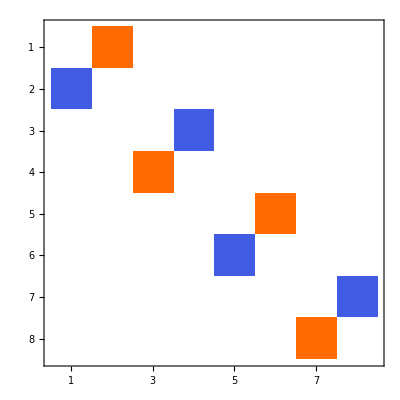
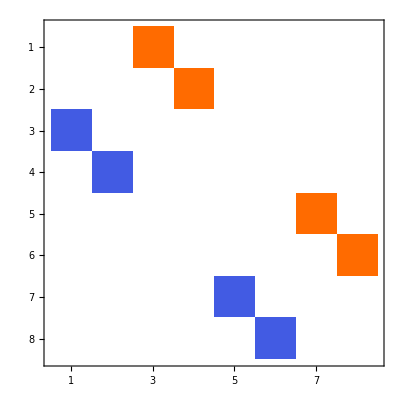
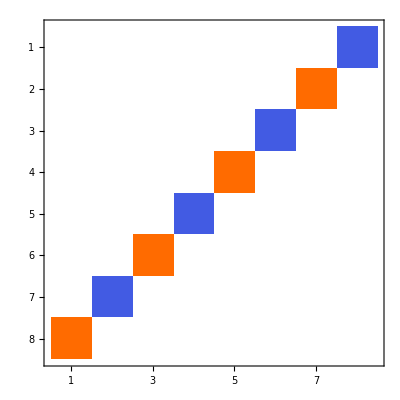
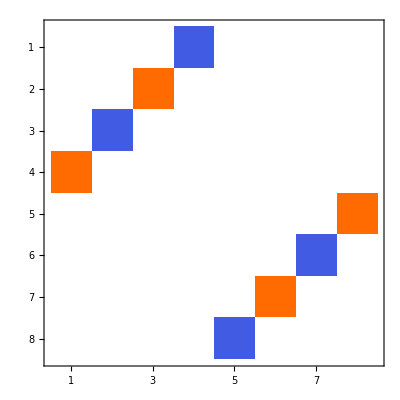
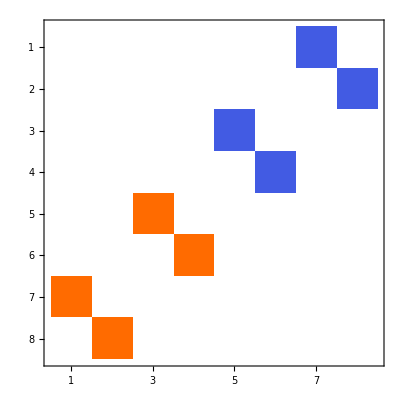
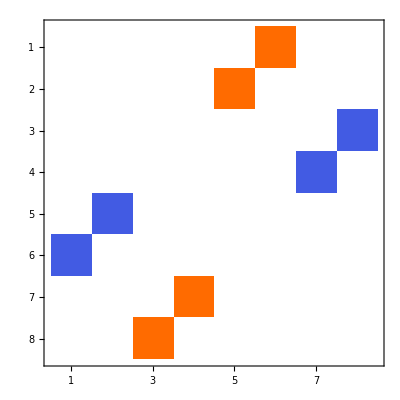

```mathematica
MatrixPlot/@vectors[testAlgebra,1]
```

where orange represents positive and blue negative numbers. Squares of the matrices gives minus unit matrix

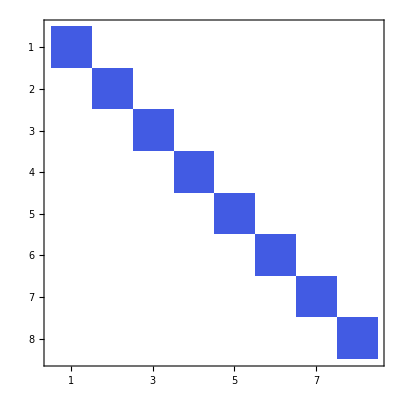
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
MatrixPlot/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

Test the interesting determinat property for vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

{(x$22922[1]^2+x$22922[2]^2+x$22922[3]^2+x$22922[4]^2+x$22922[5]^2+x$22922[6]^2)^4,(x$22922[1]^2+x$22922[2]^2+x$22922[3]^2+x$22922[4]^2+x$22922[5]^2+x$22922[6]^2)^4}

#### Cl[0,7], ->ℝ(8)⊕ℝ(8)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[0,7];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

100020200020

Base vector matrix representations. The  default setting,

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=gaAlgebraToMatrixRepresentation[testAlgebra])
```

gaAlgebraToMatrixRepresentation::NoDefaultData: No explicit default representations of elementary algebras for Cl[0,7,0] was given. Will use {{1→Diagonal,0→Antisymmetric,Cl[1,1,0]→Antisymmetric,2→IPauli[3,1],0→{Q[1,2]}},Method→{TensorProduct,QuaternionIsomorphismRules→True}} .

Base vectors of 100020are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[1, 0, 0], Cl[0, 2, 0]],{0, 1}].

Base vectors of 100020200are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[1, 0, 0], Cl[0, 2, 0], Cl[2, 0, 0]],{0, 1}].

Base vectors of 100020200020are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[1, 0, 0], Cl[0, 2, 0], Cl[2, 0, 0], Cl[0, 2, 0]],{1}].

{(0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0),(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0)}

is equivalent to

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=gaAlgebraToMatrixRepresentation[testAlgebra,{Cl[2,0]->"IPauli[3,1]",Cl[1,0]->"Diagonal",Cl[0,2]->{"Q[1,2]"}},Method ->{"TensorProduct",QuaternionIsomorphismRules->True}])
```

gaDefineInput::gaTensorProductAlgebra: gaRunningAlgebra was set to tensor product 1. Input alias of base element was disabled, it only works with Cl[p,q] algebras.

{(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0),(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0)}

The ℝ(8)⊕ℝ(8) structure is more clearly seen from

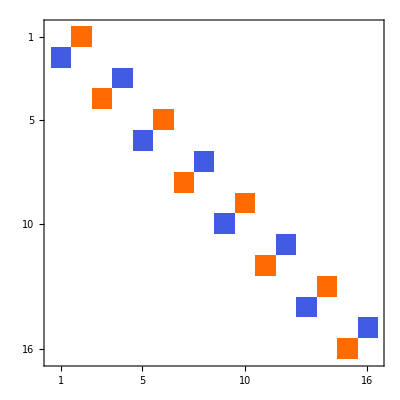
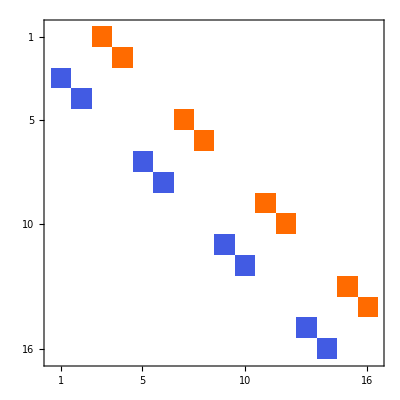
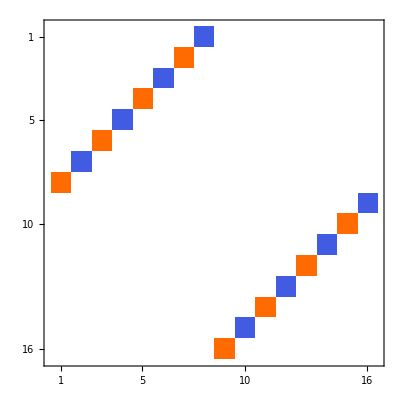
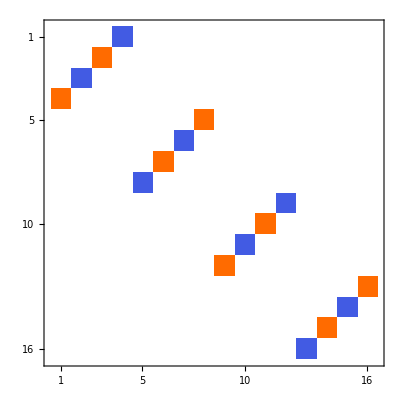
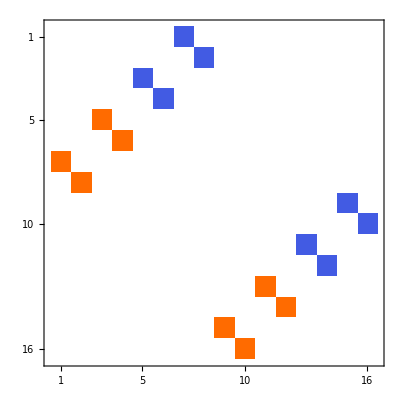
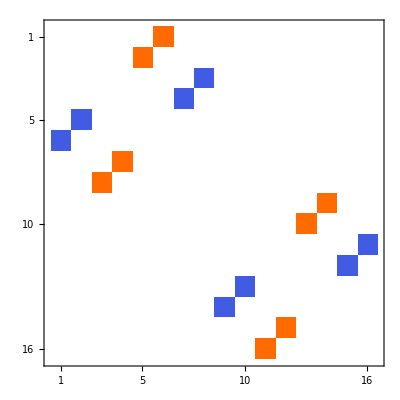
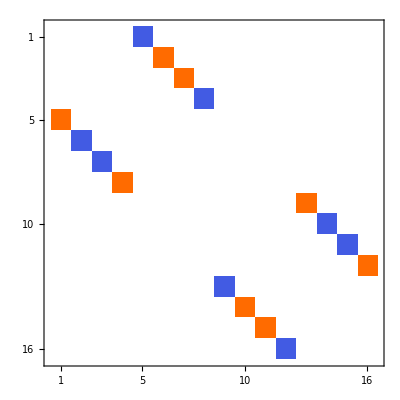

```mathematica
MatrixPlot/@vectors[testAlgebra,1]
```

These again squares to minus diagonal matrices

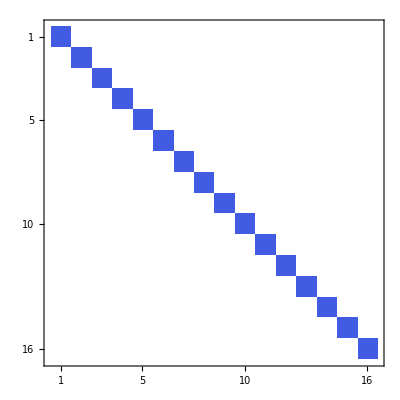
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
MatrixPlot/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

Test the interesting determinat property for vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

{(x$28575[1]^2+x$28575[2]^2+x$28575[3]^2+x$28575[4]^2+x$28575[5]^2+x$28575[6]^2+x$28575[7]^2)^8,(x$28575[1]^2+x$28575[2]^2+x$28575[3]^2+x$28575[4]^2+x$28575[5]^2+x$28575[6]^2+x$28575[7]^2)^8}

#### Cl[1,2], ->ℂ(2)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[1,2];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 21 was reached. Start picking colors randomly.

010110

Base vector matrix representations. The  default setting,

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=gaAlgebraToMatrixRepresentation[testAlgebra])
```

gaAlgebraToMatrixRepresentation::NoDefaultData: No explicit default representations of elementary algebras for Cl[1,2,0] was given. Will use {{0→Complex,1→Diagonal,1→Antisymmetric,2→Symmetric,0→Pauli[1,2]},Method→TensorProduct} .

Base vectors of 010110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[0, 1, 0], Cl[1, 1, 0]],{1}].

{(1 | 0
0 | -1),(0 | ⅈ
ⅈ | 0),(0 | 1
-1 | 0)}

is equivalent to

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=gaAlgebraToMatrixRepresentation[testAlgebra,{Cl[0,1]->"Complex",Cl[1,1]->"Antisymmetric"},Method ->"TensorProduct"])
```

gaDefineInput::gaTensorProductAlgebra: gaRunningAlgebra was set to tensor product 0. Input alias of base element was disabled, it only works with Cl[p,q] algebras.

{(1 | 0
0 | -1),(0 | 1
-1 | 0),(0 | ⅈ
ⅈ | 0)}

Test the interesting determinat property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

{-x$76539[1]^2+x$76539[2]^2+x$76539[3]^2,-x$76539[1]^2+x$76539[2]^2+x$76539[3]^2}

#### Cl[1,3], ->ℍ(2)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[1,3];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 21 was reached. Start picking colors randomly.

020110

Base vector matrix quaternionic representations.

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=gaAlgebraToMatrixRepresentation[testAlgebra])
```

gaAlgebraToMatrixRepresentation::NoDefaultData: No explicit default representations of elementary algebras for Cl[1,3,0] was given. Will use {{0→Complex,1→Diagonal,1→Antisymmetric,2→Symmetric,0→{Q[1,2]}},Method→TensorProduct} .

Base vectors of 020110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[0, 2, 0], Cl[1, 1, 0]],{1}].

{(1 | 0
0 | -1),(0 | 1020Quaternion
1020Quaternion | 0),(0 | 2020Quaternion
2020Quaternion | 0),(0 | 1
-1 | 0)}

Squares of quaternionic matrices can be calculated as

```mathematica
MatrixForm/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

gaDefineInput::gaTensorProductAlgebra: gaRunningAlgebra was set to tensor product 0. Input alias of base element was disabled, it only works with Cl[p,q] algebras.

{(1 | 0
0 | 1),(-1 | 0
0 | -1),(-1 | 0
0 | -1),(-1 | 0
0 | -1)}

Test the interesting determinat property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

{-x$81897[1]^2+x$81897[2]^2+x$81897[3]^2+x$81897[4]^2,-x$81897[1]^2+x$81897[2]^2+x$81897[3]^2+x$81897[4]^2}

Complex matrices can be calculated as

```mathematica
MatrixForm/@(vectors[testAlgebra,2]=gaAlgebraToMatrixRepresentation[testAlgebra,{Cl[1,1]->"Antisymmetric",Cl[0,2]->"Pauli[1,2]"},Method ->"TensorProduct"])
```

{(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),(0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0),(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
-1 | 0 | 0 | 0)}

```mathematica
MatrixForm/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,2])
```

{(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)}

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,2],testAlgebra,False]
```

{(x$81943[1]^2-x$81943[2]^2-x$81943[3]^2-x$81943[4]^2)^2,(x$81943[1]^2-x$81943[2]^2-x$81943[3]^2-x$81943[4]^2)^2}

Or even symbolically as (one of many variants)

```mathematica
MatrixForm/@(vectors[testAlgebra,3]=gaAlgebraToMatrixRepresentation[testAlgebra,{Cl[1,1]->"Trigonometric",Cl[0,2]->"HyperbolicTrigonometric"},Method ->"TensorProduct"]//Simplify)
```

{(Sin[φ$81963] | Cos[φ$81963] | 0 | 0
Cos[φ$81963] | -Sin[φ$81963] | 0 | 0
0 | 0 | Sin[φ$81963] | Cos[φ$81963]
0 | 0 | Cos[φ$81963] | -Sin[φ$81963]),(-ⅈ Cos[φ$81963] | ⅈ Sin[φ$81963] | 0 | 0
ⅈ Sin[φ$81963] | ⅈ Cos[φ$81963] | 0 | 0
0 | 0 | -ⅈ Cos[φ$81963] | ⅈ Sin[φ$81963]
0 | 0 | ⅈ Sin[φ$81963] | ⅈ Cos[φ$81963]),(0 | -ⅈ Sinh[φ$81955] | 0 | Cosh[φ$81955]
ⅈ Sinh[φ$81955] | 0 | -Cosh[φ$81955] | 0
0 | Cosh[φ$81955] | 0 | ⅈ Sinh[φ$81955]
-Cosh[φ$81955] | 0 | -ⅈ Sinh[φ$81955] | 0),(0 | Cosh[φ$81955] | 0 | ⅈ Sinh[φ$81955]
-Cosh[φ$81955] | 0 | -ⅈ Sinh[φ$81955] | 0
0 | ⅈ Sinh[φ$81955] | 0 | -Cosh[φ$81955]
-ⅈ Sinh[φ$81955] | 0 | Cosh[φ$81955] | 0)}

```mathematica
MatrixForm/@Simplify[(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,3])]
```

{(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)}

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,3],testAlgebra,False]
```

{(x$81996[1]^2-x$81996[2]^2-x$81996[3]^2-x$81996[4]^2)^2,(x$81996[1]^2-x$81996[2]^2-x$81996[3]^2-x$81996[4]^2)^2}

#### Cl[1,4], ->ℍ(2)⊕ℍ(2)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[1,4];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 21 was reached. Start picking colors randomly.

100020110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=gaAlgebraToMatrixRepresentation[testAlgebra])
```

gaAlgebraToMatrixRepresentation::NoDefaultData: No explicit default representations of elementary algebras for Cl[1,4,0] was given. Will use {{0→Complex,1→Diagonal,1→Antisymmetric,2→Symmetric,0→{Q[1,2]}},Method→TensorProduct} .

Base vectors of 100020are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[1, 0, 0], Cl[0, 2, 0]],{0, 1}].

Base vectors of 100020110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[1, 0, 0], Cl[0, 2, 0], Cl[1, 1, 0]],{1}].

{(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),(0 | 1020Quaternion | 0 | 0
1020Quaternion | 0 | 0 | 0
0 | 0 | 0 | 1020Quaternion
0 | 0 | 1020Quaternion | 0),(0 | 2020Quaternion | 0 | 0
2020Quaternion | 0 | 0 | 0
0 | 0 | 0 | 2020Quaternion
0 | 0 | 2020Quaternion | 0),(0 | 12020Quaternion | 0 | 0
12020Quaternion | 0 | 0 | 0
0 | 0 | 0 | -12020Quaternion
0 | 0 | -12020Quaternion | 0),(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0)}

Test the interesting determinant property for vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

gaDefineInput::gaTensorProductAlgebra: gaRunningAlgebra was set to tensor product 1. Input alias of base element was disabled, it only works with Cl[p,q] algebras.

{(x$87382[1]^2-x$87382[2]^2-x$87382[3]^2-x$87382[4]^2-x$87382[5]^2)^2,(x$87382[1]^2-x$87382[2]^2-x$87382[3]^2-x$87382[4]^2-x$87382[5]^2)^2}

#### Cl[1,5], ->ℍ(4)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[1,5];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 21 was reached. Start picking colors randomly.

200020110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=gaAlgebraToMatrixRepresentation[testAlgebra])
```

gaAlgebraToMatrixRepresentation::NoDefaultData: No explicit default representations of elementary algebras for Cl[1,5,0] was given. Will use {{0→Complex,1→Diagonal,1→Antisymmetric,2→Symmetric,0→{Q[1,2]}},Method→TensorProduct} .

Base vectors of 200020are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[2, 0, 0], Cl[0, 2, 0]],{0, 1}].

Base vectors of 200020110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[2, 0, 0], Cl[0, 2, 0], Cl[1, 1, 0]],{1}].

{(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),(0 | 1020Quaternion | 0 | 0
1020Quaternion | 0 | 0 | 0
0 | 0 | 0 | 1020Quaternion
0 | 0 | 1020Quaternion | 0),(0 | 2020Quaternion | 0 | 0
2020Quaternion | 0 | 0 | 0
0 | 0 | 0 | 2020Quaternion
0 | 0 | 2020Quaternion | 0),(0 | 12020Quaternion | 0 | 0
12020Quaternion | 0 | 0 | 0
0 | 0 | 0 | -12020Quaternion
0 | 0 | -12020Quaternion | 0),(0 | 0 | 0 | 12020Quaternion
0 | 0 | 12020Quaternion | 0
0 | 12020Quaternion | 0 | 0
12020Quaternion | 0 | 0 | 0),(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0)}

Squares of quaternionic matrices can be calculated as

```mathematica
MatrixForm/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

gaDefineInput::gaTensorProductAlgebra: gaRunningAlgebra was set to tensor product 2. Input alias of base element was disabled, it only works with Cl[p,q] algebras.

{(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)}

Test the interesting determinat property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

{(x$92800[1]^2-x$92800[2]^2-x$92800[3]^2-x$92800[4]^2-x$92800[5]^2-x$92800[6]^2)^2,(x$92800[1]^2-x$92800[2]^2-x$92800[3]^2-x$92800[4]^2-x$92800[5]^2-x$92800[6]^2)^2}

#### Cl[1,6], ->ℂ(8)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[1,6];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 21 was reached. Start picking colors randomly.

010200020110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=gaAlgebraToMatrixRepresentation[testAlgebra])
```

gaAlgebraToMatrixRepresentation::NoDefaultData: No explicit default representations of elementary algebras for Cl[1,6,0] was given. Will use {{0→Complex,1→Diagonal,1→Antisymmetric,2→Symmetric,0→Pauli[1,2]},Method→TensorProduct} .

Base vectors of 010200are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[0, 1, 0], Cl[2, 0, 0]],{0, 1}].

Base vectors of 010200020are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[0, 1, 0], Cl[2, 0, 0], Cl[0, 2, 0]],{0, 1}].

Base vectors of 010200020110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[0, 1, 0], Cl[2, 0, 0], Cl[0, 2, 0], Cl[1, 1, 0]],{1}].

{(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0
ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0
0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ
0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0
0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0
ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ
0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0
0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0
0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ
0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0
0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0
0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0
0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0
ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)}

Squares of  matrices can be calculated as

```mathematica
MatrixForm/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

gaDefineInput::gaTensorProductAlgebra: gaRunningAlgebra was set to tensor product 0. Input alias of base element was disabled, it only works with Cl[p,q] algebras.

{(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)}

Test the interesting determinat property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

{(x$98236[1]^2-x$98236[2]^2-x$98236[3]^2-x$98236[4]^2-x$98236[5]^2-x$98236[6]^2-x$98236[7]^2)^4,(x$98236[1]^2-x$98236[2]^2-x$98236[3]^2-x$98236[4]^2-x$98236[5]^2-x$98236[6]^2-x$98236[7]^2)^4}

#### Cl[1,7], ->ℝ(16)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[1,7];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 21 was reached. Start picking colors randomly.

020200020110

Base vector matrix representations using default settings

gaAlgebraToMatrixRepresentation::NoDefaultData: No explicit default representations of elementary algebras for Cl[1,7,0] was given. Will use {{1→Diagonal,0→Antisymmetric,1→Antisymmetric,2→IPauli[3,1],0→{Q[1,2]}},Method→{TensorProduct,QuaternionIsomorphismRules→True}} .

Base vectors of 020200are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[0, 2, 0], Cl[2, 0, 0]],{0, 1}].

Base vectors of 020200020are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[0, 2, 0], Cl[2, 0, 0], Cl[0, 2, 0]],{0, 1}].

Base vectors of 020200020110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[0, 2, 0], Cl[2, 0, 0], Cl[0, 2, 0], Cl[1, 1, 0]],{1}].

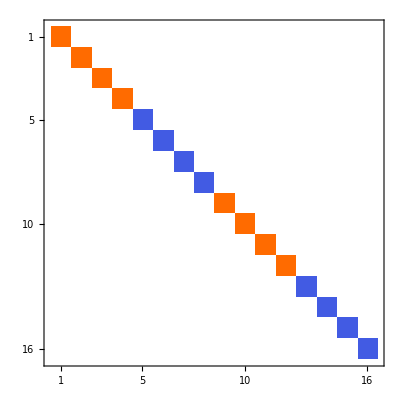
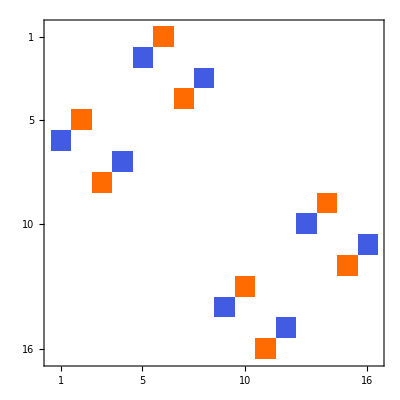
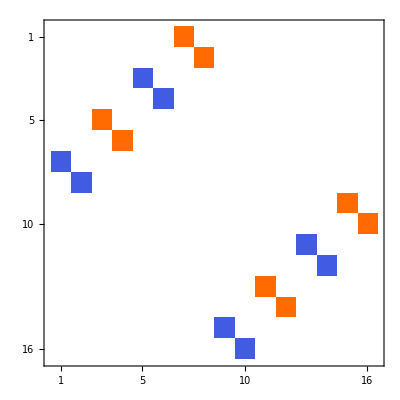
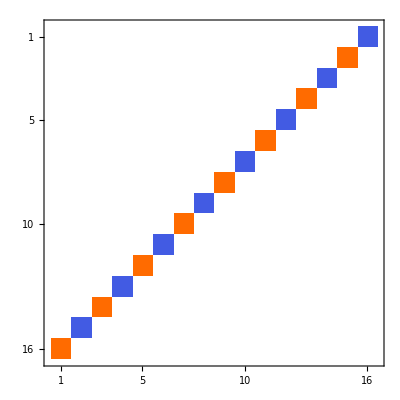
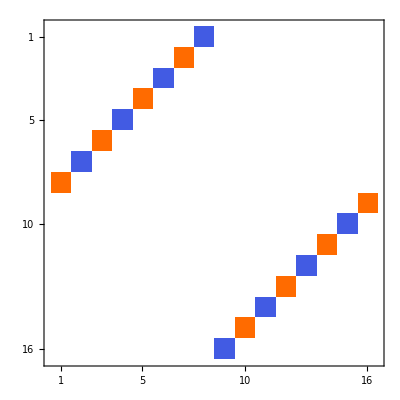
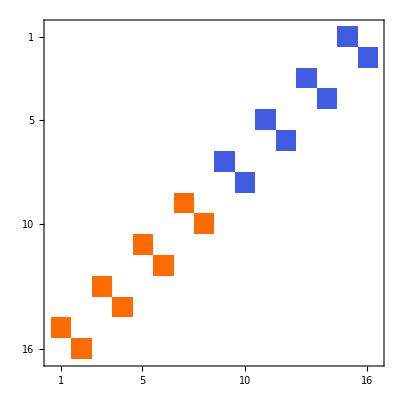
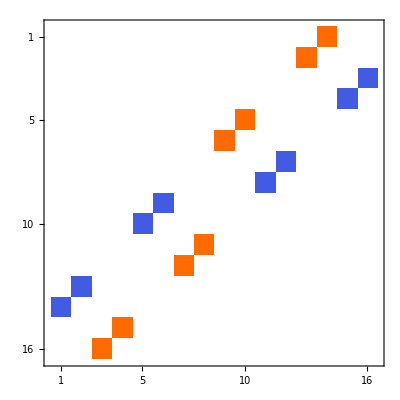
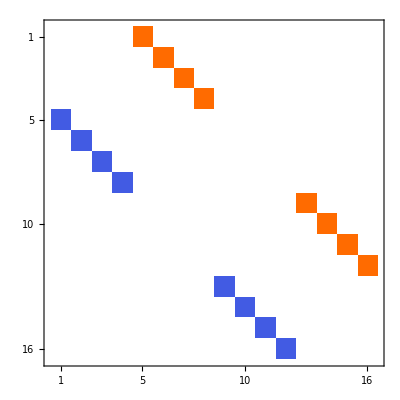

```mathematica
MatrixPlot/@(vectors[testAlgebra,1]=gaAlgebraToMatrixRepresentation[testAlgebra])
```

We can make them sparse with

```mathematica
vectors[testAlgebra,2]=SparseArray/@vectors[testAlgebra,1]
```

gaDefineInput::gaTensorProductAlgebra: gaRunningAlgebra was set to tensor product 0. Input alias of base element was disabled, it only works with Cl[p,q] algebras.

{SparseArray[<16>, {16, 16}],SparseArray[<16>, {16, 16}],SparseArray[<16>, {16, 16}],SparseArray[<16>, {16, 16}],SparseArray[<16>, {16, 16}],SparseArray[<16>, {16, 16}],SparseArray[<16>, {16, 16}],SparseArray[<16>, {16, 16}]}

Squares of sparse matrices can be calculated using Dot[ ]. Unfortunatelly gaGeometricMatrixProduct[ ] would expand them to dense matrix and it will take much more time to multiply

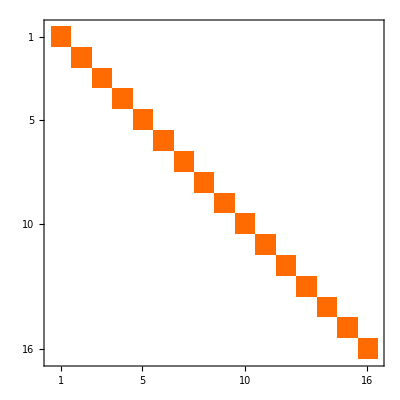
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
MatrixPlot/@(Dot[#,#]&/@vectors[testAlgebra,2])
```

Test the interesting determinat property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

{(x$105159[1]^2-x$105159[2]^2-x$105159[3]^2-x$105159[4]^2-x$105159[5]^2-x$105159[6]^2-x$105159[7]^2-x$105159[8]^2)^8,(x$105159[1]^2-x$105159[2]^2-x$105159[3]^2-x$105159[4]^2-x$105159[5]^2-x$105159[6]^2-x$105159[7]^2-x$105159[8]^2)^8}

#### Cl[2,1], ->ℝ(2)⊕ℝ(2)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[2,1];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 21 was reached. Start picking colors randomly.

100110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=gaAlgebraToMatrixRepresentation[testAlgebra])
```

gaAlgebraToMatrixRepresentation::NoDefaultData: No explicit default representations of elementary algebras for Cl[2,1,0] was given. Will use {{1→Diagonal,0→Antisymmetric,1→Antisymmetric,2→IPauli[3,1],0→{Q[1,2]}},Method→{TensorProduct,QuaternionIsomorphismRules→True}} .

Base vectors of 100110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[1, 0, 0], Cl[1, 1, 0]],{1}].

gaAlgebraToMatrixRepresentation::smaller: Tensor product decomposition 1 contains Cl[1,0] algebra. Smaller (complex) representation matrices can be obtained using Method ->{"TensorProduct",BaseVectorAlgebra→1,TargetMatrices→Reals}. The smaller matrices realizes HOMOMORPHISM of the algebra (not an isomorphism).

{(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -1 | 0),(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0)}

There exist, however 2×2 dimensional real representation!

```mathematica
MatrixForm/@(vectors[testAlgebra,2]=gaAlgebraToMatrixRepresentation[testAlgebra,{Cl[0,1]->"Complex",Cl[1,1]->"Antisymmetric"},Method ->{"TensorProduct",BaseVectorAlgebra->120,TargetMatrices->Reals}])
```

gaDefineInput::gaTensorProductAlgebra: gaRunningAlgebra was set to tensor product 1. Input alias of base element was disabled, it only works with Cl[p,q] algebras.

{(0 | -1
-1 | 0),(1 | 0
0 | -1),(0 | 1
-1 | 0)}

Squares of sparse matrices can be calculated using Dot[ ]. Unfortunatelly gaGeometricMatrixProduct[ ] would expand them to dense matrix and it will take much more time to multiply

```mathematica
MatrixForm/@(Dot[#,#]&/@vectors[testAlgebra,1])
```

{(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)}

```mathematica
MatrixForm/@(Dot[#,#]&/@vectors[testAlgebra,2])
```

{(1 | 0
0 | 1),(1 | 0
0 | 1),(-1 | 0
0 | -1)}

Test the interesting determinat property for both vectors representations (note the difference in powers)

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

{(x$112299[1]^2+x$112299[2]^2-x$112299[3]^2)^2,(x$112299[1]^2+x$112299[2]^2-x$112299[3]^2)^2}

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,2],testAlgebra,False]
```

{-x$112305[1]^2-x$112305[2]^2+x$112305[3]^2,-x$112305[1]^2-x$112305[2]^2+x$112305[3]^2}

#### Cl[2,2], ->ℝ(4)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[2,2];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 21 was reached. Start picking colors randomly.

110110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=gaAlgebraToMatrixRepresentation[testAlgebra])
```

gaAlgebraToMatrixRepresentation::NoDefaultData: No explicit default representations of elementary algebras for Cl[2,2,0] was given. Will use {{1→Diagonal,0→Antisymmetric,1→Antisymmetric,2→IPauli[3,1],0→{Q[1,2]}},Method→{TensorProduct,QuaternionIsomorphismRules→True}} .

Base vectors of 110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[1, 1, 0], Cl[1, 1, 0]],{1}].

{(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -1 | 0),(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
-1 | 0 | 0 | 0),(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0)}

Squares of sparse matrices can be calculated using Dot[ ]. Unfortunatelly gaGeometricMatrixProduct[ ] would expand them to dense matrix and it will take much more time to multiply

```mathematica
MatrixForm/@(Dot[#,#]&/@vectors[testAlgebra,1])
```

gaDefineInput::gaTensorProductAlgebra: gaRunningAlgebra was set to tensor product 1. Input alias of base element was disabled, it only works with Cl[p,q] algebras.

{(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)}

Test the interesting determinat property for vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

{(x$117651[1]^2+x$117651[2]^2-x$117651[3]^2-x$117651[4]^2)^2,(x$117651[1]^2+x$117651[2]^2-x$117651[3]^2-x$117651[4]^2)^2}

#### Cl[2,3], ->ℂ(4)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[2,3];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 21 was reached. Start picking colors randomly.

010110110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=gaAlgebraToMatrixRepresentation[testAlgebra])
```

gaAlgebraToMatrixRepresentation::NoDefaultData: No explicit default representations of elementary algebras for Cl[2,3,0] was given. Will use {{0→Complex,1→Diagonal,1→Antisymmetric,2→Symmetric,0→Pauli[1,2]},Method→TensorProduct} .

Base vectors of 010110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[0, 1, 0], Cl[1, 1, 0]],{0, 1}].

Base vectors of 010110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[0, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{1}].

{(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -1 | 0),(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
-1 | 0 | 0 | 0),(0 | 0 | 0 | ⅈ
0 | 0 | ⅈ | 0
0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0),(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0)}

Squares of sparse matrices can be calculated using Dot[ ]. Unfortunatelly gaGeometricMatrixProduct[ ] would expand them to dense matrix and it will take much more time to multiply

```mathematica
MatrixForm/@(Dot[#,#]&/@vectors[testAlgebra,1])
```

gaDefineInput::gaTensorProductAlgebra: gaRunningAlgebra was set to tensor product 0. Input alias of base element was disabled, it only works with Cl[p,q] algebras.

{(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)}

Test the interesting determinat property for vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

{(x$123024[1]^2+x$123024[2]^2-x$123024[3]^2-x$123024[4]^2-x$123024[5]^2)^2,(x$123024[1]^2+x$123024[2]^2-x$123024[3]^2-x$123024[4]^2-x$123024[5]^2)^2}

#### Cl[2,4], ->ℍ(4)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[2,4];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 21 was reached. Start picking colors randomly.

020110110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=gaAlgebraToMatrixRepresentation[testAlgebra])
```

gaAlgebraToMatrixRepresentation::NoDefaultData: No explicit default representations of elementary algebras for Cl[2,4,0] was given. Will use {{0→Complex,1→Diagonal,1→Antisymmetric,2→Symmetric,0→{Q[1,2]}},Method→TensorProduct} .

Base vectors of 020110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[0, 2, 0], Cl[1, 1, 0]],{0, 1}].

Base vectors of 020110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[0, 2, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{1}].

{(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -1 | 0),(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
-1 | 0 | 0 | 0),(0 | 0 | 0 | 1020Quaternion
0 | 0 | 1020Quaternion | 0
0 | 1020Quaternion | 0 | 0
1020Quaternion | 0 | 0 | 0),(0 | 0 | 0 | 2020Quaternion
0 | 0 | 2020Quaternion | 0
0 | 2020Quaternion | 0 | 0
2020Quaternion | 0 | 0 | 0),(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0)}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ]. Note, that Dot[ ] don’t know how to multiply quaternions

```mathematica
MatrixForm/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

gaDefineInput::gaTensorProductAlgebra: gaRunningAlgebra was set to tensor product 0. Input alias of base element was disabled, it only works with Cl[p,q] algebras.

{(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)}

Test the interesting determinat property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

{(x$128436[1]^2+x$128436[2]^2-x$128436[3]^2-x$128436[4]^2-x$128436[5]^2-x$128436[6]^2)^2,(x$128436[1]^2+x$128436[2]^2-x$128436[3]^2-x$128436[4]^2-x$128436[5]^2-x$128436[6]^2)^2}

#### Cl[2,5], ->ℍ(4)⊕ℍ(4)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[2,5];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 21 was reached. Start picking colors randomly.

100020110110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=gaAlgebraToMatrixRepresentation[testAlgebra])
```

gaAlgebraToMatrixRepresentation::NoDefaultData: No explicit default representations of elementary algebras for Cl[2,5,0] was given. Will use {{0→Complex,1→Diagonal,1→Antisymmetric,2→Symmetric,0→{Q[1,2]}},Method→TensorProduct} .

Base vectors of 100020are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[1, 0, 0], Cl[0, 2, 0]],{0, 1}].

Base vectors of 100020110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[1, 0, 0], Cl[0, 2, 0], Cl[1, 1, 0]],{0, 1}].

Base vectors of 100020110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[1, 0, 0], Cl[0, 2, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{1}].

{(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0
0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0
0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0
0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0),(0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0
0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0
0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0
0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0),(0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0
0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion | 0
0 | 0 | 0 | 0 | 0 | -12020Quaternion | 0 | 0
0 | 0 | 0 | 0 | -12020Quaternion | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ]. Note, that Dot[ ] don’t know how to multiply quaternions

gaDefineInput::gaTensorProductAlgebra: gaRunningAlgebra was set to tensor product 1. Input alias of base element was disabled, it only works with Cl[p,q] algebras.

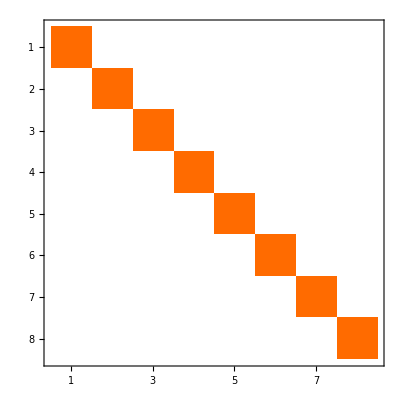
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
MatrixPlot/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

Test the interesting determinat property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

{(x$134443[1]^2+x$134443[2]^2-x$134443[3]^2-x$134443[4]^2-x$134443[5]^2-x$134443[6]^2-x$134443[7]^2)^4,(x$134443[1]^2+x$134443[2]^2-x$134443[3]^2-x$134443[4]^2-x$134443[5]^2-x$134443[6]^2-x$134443[7]^2)^4}

#### Cl[2,6], ->ℍ(8)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[2,6];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 21 was reached. Start picking colors randomly.

200020110110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=gaAlgebraToMatrixRepresentation[testAlgebra])
```

gaAlgebraToMatrixRepresentation::NoDefaultData: No explicit default representations of elementary algebras for Cl[2,6,0] was given. Will use {{0→Complex,1→Diagonal,1→Antisymmetric,2→Symmetric,0→{Q[1,2]}},Method→TensorProduct} .

Base vectors of 200020are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[2, 0, 0], Cl[0, 2, 0]],{0, 1}].

Base vectors of 200020110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[2, 0, 0], Cl[0, 2, 0], Cl[1, 1, 0]],{0, 1}].

Base vectors of 200020110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[2, 0, 0], Cl[0, 2, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{1}].

{(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0
0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0
0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0
0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0),(0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0
0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0
0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0
0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0),(0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0
0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion | 0
0 | 0 | 0 | 0 | 0 | -12020Quaternion | 0 | 0
0 | 0 | 0 | 0 | -12020Quaternion | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 12020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | 12020Quaternion | 0
0 | 0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0
0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0
0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0
0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ]. Note, that Dot[ ] don’t know how to multiply quaternions

```mathematica
MatrixForm/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

gaDefineInput::gaTensorProductAlgebra: gaRunningAlgebra was set to tensor product 2. Input alias of base element was disabled, it only works with Cl[p,q] algebras.

{(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)}

Test the interesting determinat property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

{(x$139933[1]^2+x$139933[2]^2-x$139933[3]^2-x$139933[4]^2-x$139933[5]^2-x$139933[6]^2-x$139933[7]^2-x$139933[8]^2)^4,(x$139933[1]^2+x$139933[2]^2-x$139933[3]^2-x$139933[4]^2-x$139933[5]^2-x$139933[6]^2-x$139933[7]^2-x$139933[8]^2)^4}

#### Cl[2,7], ->ℂ(16)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[2,7];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 21 was reached. Start picking colors randomly.

010200020110110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=gaAlgebraToMatrixRepresentation[testAlgebra])
```

gaAlgebraToMatrixRepresentation::NoDefaultData: No explicit default representations of elementary algebras for Cl[2,7,0] was given. Will use {{0→Complex,1→Diagonal,1→Antisymmetric,2→Symmetric,0→Pauli[1,2]},Method→TensorProduct} .

Base vectors of 010200are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[0, 1, 0], Cl[2, 0, 0]],{0, 1}].

Base vectors of 010200020are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[0, 1, 0], Cl[2, 0, 0], Cl[0, 2, 0]],{0, 1}].

Base vectors of 010200020110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[0, 1, 0], Cl[2, 0, 0], Cl[0, 2, 0], Cl[1, 1, 0]],{0, 1}].

Base vectors of 010200020110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[0, 1, 0], Cl[2, 0, 0], Cl[0, 2, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{1}].

{(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ]. Note, that Dot[ ] don’t know how to multiply quaternions

```mathematica
MatrixPlot/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

gaDefineInput::gaTensorProductAlgebra: gaRunningAlgebra was set to tensor product 0. Input alias of base element was disabled, it only works with Cl[p,q] algebras.

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Test the interesting determinat property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

{(x$145978[1]^2+x$145978[2]^2-x$145978[3]^2-x$145978[4]^2-x$145978[5]^2-x$145978[6]^2-x$145978[7]^2-x$145978[8]^2-x$145978[9]^2)^8,(x$145978[1]^2+x$145978[2]^2-x$145978[3]^2-x$145978[4]^2-x$145978[5]^2-x$145978[6]^2-x$145978[7]^2-x$145978[8]^2-x$145978[9]^2)^8}

#### Cl[3,0], ->ℂ(2)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[3,0];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

010200

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=gaAlgebraToMatrixRepresentation[testAlgebra])
```

gaAlgebraToMatrixRepresentation::NoDefaultData: No explicit default representations of elementary algebras for 3 was given. Will use {{0→Complex,1→Diagonal,1→Antisymmetric,2→Symmetric,0→Pauli[1,2]},Method→TensorProduct} .

{(1 | 0
0 | -1),(0 | 1
1 | 0),(0 | ⅈ
-ⅈ | 0)}

Base vector matrix representations using symbolic matrix. Possible  types are "Trigonometric"
"TrigonometricAntisymmetric"
"HyperbolicTrigonometric"
"HyperbolicTrigonometricAntisymmetric"

```mathematica
MatrixForm/@(vectors[testAlgebra,2]=gaAlgebraToMatrixRepresentation[testAlgebra,{010->"Complex",200->"Trigonometric"},Method->"TensorProduct"])
```

{(Sin[φ$147810] | Cos[φ$147810]
Cos[φ$147810] | -Sin[φ$147810]),(-Cos[φ$147810] | Sin[φ$147810]
Sin[φ$147810] | Cos[φ$147810]),(0 | ⅈ (Cos[φ$147810]^2+Sin[φ$147810]^2)
ⅈ (-Cos[φ$147810]^2-Sin[φ$147810]^2) | 0)}

```mathematica
MatrixForm/@(vectors[testAlgebra,2]//Simplify)
```

{(Sin[φ$147810] | Cos[φ$147810]
Cos[φ$147810] | -Sin[φ$147810]),(-Cos[φ$147810] | Sin[φ$147810]
Sin[φ$147810] | Cos[φ$147810]),(0 | ⅈ
-ⅈ | 0)}

The other form is

```mathematica
MatrixForm/@(vectors[testAlgebra,3]=gaAlgebraToMatrixRepresentation[testAlgebra,{010->"Complex",200->"HyperbolicTrigonometric"},Method->"TensorProduct"])
```

{(-ⅈ Sinh[φ$147853] | Cosh[φ$147853]
Cosh[φ$147853] | ⅈ Sinh[φ$147853]),(Cosh[φ$147853] | ⅈ Sinh[φ$147853]
ⅈ Sinh[φ$147853] | -Cosh[φ$147853]),(0 | ⅈ (-Cosh[φ$147853]^2+Sinh[φ$147853]^2)
ⅈ (Cosh[φ$147853]^2-Sinh[φ$147853]^2) | 0)}

```mathematica
MatrixForm/@(vectors[testAlgebra,3]//Simplify)
```

{(-ⅈ Sinh[φ$147853] | Cosh[φ$147853]
Cosh[φ$147853] | ⅈ Sinh[φ$147853]),(Cosh[φ$147853] | ⅈ Sinh[φ$147853]
ⅈ Sinh[φ$147853] | -Cosh[φ$147853]),(0 | -ⅈ
ⅈ | 0)}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixForm/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{(1 | 0
0 | 1),(1 | 0
0 | 1),(1 | 0
0 | 1)}

```mathematica
MatrixForm/@(Simplify[gaGeometricMatrixProduct[#,#]]&/@vectors[testAlgebra,2])
```

{(1 | 0
0 | 1),(1 | 0
0 | 1),(1 | 0
0 | 1)}

```mathematica
MatrixForm/@(Simplify[gaGeometricMatrixProduct[#,#]]&/@vectors[testAlgebra,3])
```

{(1 | 0
0 | 1),(1 | 0
0 | 1),(1 | 0
0 | 1)}

Test the interesting determinat property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

{-x$147893[1]^2-x$147893[2]^2-x$147893[3]^2,-x$147893[1]^2-x$147893[2]^2-x$147893[3]^2}

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,2],testAlgebra,False]
```

{-x$147894[1]^2-x$147894[2]^2-x$147894[3]^2,-x$147894[1]^2-x$147894[2]^2-x$147894[3]^2}

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,3],testAlgebra,False]
```

{-x$147895[1]^2-x$147895[2]^2-x$147895[3]^2,-x$147895[1]^2-x$147895[2]^2-x$147895[3]^2}

#### Cl[3,1], ->ℝ(4)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[3,1];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 21 was reached. Start picking colors randomly.

200110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=gaAlgebraToMatrixRepresentation[testAlgebra])
```

gaAlgebraToMatrixRepresentation::NoDefaultData: No explicit default representations of elementary algebras for Cl[3,1,0] was given. Will use {{1→Diagonal,0→Antisymmetric,1→Antisymmetric,2→IPauli[3,1],0→{Q[1,2]}},Method→{TensorProduct,QuaternionIsomorphismRules→True}} .

Base vectors of 200110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[2, 0, 0], Cl[1, 1, 0]],{1}].

{(0 | 0 | 0 | -1
0 | 0 | -1 | 0
0 | -1 | 0 | 0
-1 | 0 | 0 | 0),(0 | -1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0),(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0)}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ]. Note, that Dot[ ] don’t know how to multiply quaternions

```mathematica
MatrixForm/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

gaDefineInput::gaTensorProductAlgebra: gaRunningAlgebra was set to tensor product 2. Input alias of base element was disabled, it only works with Cl[p,q] algebras.

{(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)}

Test the interesting determinat property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

{(x$153235[1]^2+x$153235[2]^2+x$153235[3]^2-x$153235[4]^2)^2,(x$153235[1]^2+x$153235[2]^2+x$153235[3]^2-x$153235[4]^2)^2}

#### Cl[3,2], ->ℝ(4)⊕ℝ(4)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[3,2];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 21 was reached. Start picking colors randomly.

100110110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=gaAlgebraToMatrixRepresentation[testAlgebra])
```

gaAlgebraToMatrixRepresentation::NoDefaultData: No explicit default representations of elementary algebras for Cl[3,2,0] was given. Will use {{1→Diagonal,0→Antisymmetric,1→Antisymmetric,2→IPauli[3,1],0→{Q[1,2]}},Method→{TensorProduct,QuaternionIsomorphismRules→True}} .

Base vectors of 100110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[1, 0, 0], Cl[1, 1, 0]],{0, 1}].

Base vectors of 100110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[1, 0, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{1}].

gaAlgebraToMatrixRepresentation::smaller: Tensor product decomposition 1 contains Cl[1,0] algebra. Smaller (complex) representation matrices can be obtained using Method ->{"TensorProduct",BaseVectorAlgebra→2,TargetMatrices→Reals}. The smaller matrices realizes HOMOMORPHISM of the algebra (not an isomorphism).

{(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ]. Note, that Dot[ ] don’t know how to multiply quaternions

```mathematica
MatrixForm/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

gaDefineInput::gaTensorProductAlgebra: gaRunningAlgebra was set to tensor product 1. Input alias of base element was disabled, it only works with Cl[p,q] algebras.

{(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)}

Test the interesting determinat property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

{(x$160371[1]^2+x$160371[2]^2+x$160371[3]^2-x$160371[4]^2-x$160371[5]^2)^4,(x$160371[1]^2+x$160371[2]^2+x$160371[3]^2-x$160371[4]^2-x$160371[5]^2)^4}

#### Cl[3,3], ->ℝ(8)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[3,3];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 21 was reached. Start picking colors randomly.

110110110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=gaAlgebraToMatrixRepresentation[testAlgebra])
```

gaAlgebraToMatrixRepresentation::NoDefaultData: No explicit default representations of elementary algebras for Cl[3,3,0] was given. Will use {{1→Diagonal,0→Antisymmetric,1→Antisymmetric,2→IPauli[3,1],0→{Q[1,2]}},Method→{TensorProduct,QuaternionIsomorphismRules→True}} .

Base vectors of 110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[1, 1, 0], Cl[1, 1, 0]],{0, 1}].

Base vectors of 110110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{1}].

{(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ]. Note, that Dot[ ] don’t know how to multiply quaternions

```mathematica
MatrixForm/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

gaDefineInput::gaTensorProductAlgebra: gaRunningAlgebra was set to tensor product 1. Input alias of base element was disabled, it only works with Cl[p,q] algebras.

{(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)}

Test the interesting determinat property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

{(x$165764[1]^2+x$165764[2]^2+x$165764[3]^2-x$165764[4]^2-x$165764[5]^2-x$165764[6]^2)^4,(x$165764[1]^2+x$165764[2]^2+x$165764[3]^2-x$165764[4]^2-x$165764[5]^2-x$165764[6]^2)^4}

#### Cl[3,4], ->ℂ(8)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[3,4];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 21 was reached. Start picking colors randomly.

010110110110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=gaAlgebraToMatrixRepresentation[testAlgebra])
```

gaAlgebraToMatrixRepresentation::NoDefaultData: No explicit default representations of elementary algebras for Cl[3,4,0] was given. Will use {{0→Complex,1→Diagonal,1→Antisymmetric,2→Symmetric,0→Pauli[1,2]},Method→TensorProduct} .

Base vectors of 010110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[0, 1, 0], Cl[1, 1, 0]],{0, 1}].

Base vectors of 010110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[0, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{0, 1}].

Base vectors of 010110110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[0, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{1}].

{(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ
0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0
0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0
0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0
0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0
ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ]. Note, that Dot[ ] don’t know how to multiply quaternions

```mathematica
MatrixForm/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

gaDefineInput::gaTensorProductAlgebra: gaRunningAlgebra was set to tensor product 0. Input alias of base element was disabled, it only works with Cl[p,q] algebras.

{(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)}

Test the interesting determinat property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

{(x$171190[1]^2+x$171190[2]^2+x$171190[3]^2-x$171190[4]^2-x$171190[5]^2-x$171190[6]^2-x$171190[7]^2)^4,(x$171190[1]^2+x$171190[2]^2+x$171190[3]^2-x$171190[4]^2-x$171190[5]^2-x$171190[6]^2-x$171190[7]^2)^4}

#### Cl[3,5], ->ℍ(8)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[3,5];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 21 was reached. Start picking colors randomly.

020110110110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=gaAlgebraToMatrixRepresentation[testAlgebra])
```

gaAlgebraToMatrixRepresentation::NoDefaultData: No explicit default representations of elementary algebras for Cl[3,5,0] was given. Will use {{0→Complex,1→Diagonal,1→Antisymmetric,2→Symmetric,0→{Q[1,2]}},Method→TensorProduct} .

Base vectors of 020110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[0, 2, 0], Cl[1, 1, 0]],{0, 1}].

Base vectors of 020110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[0, 2, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{0, 1}].

Base vectors of 020110110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[0, 2, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{1}].

{(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0
0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0
0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0
0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0
0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0
0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0
0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0
0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0
0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ]. Note, that Dot[ ] don’t know how to multiply quaternions

```mathematica
MatrixForm/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

gaDefineInput::gaTensorProductAlgebra: gaRunningAlgebra was set to tensor product 0. Input alias of base element was disabled, it only works with Cl[p,q] algebras.

{(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)}

Test the interesting determinat property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

{(x$176677[1]^2+x$176677[2]^2+x$176677[3]^2-x$176677[4]^2-x$176677[5]^2-x$176677[6]^2-x$176677[7]^2-x$176677[8]^2)^4,(x$176677[1]^2+x$176677[2]^2+x$176677[3]^2-x$176677[4]^2-x$176677[5]^2-x$176677[6]^2-x$176677[7]^2-x$176677[8]^2)^4}

#### Cl[3,6], ->ℍ(8)⊕ℍ(8)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[3,6];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 21 was reached. Start picking colors randomly.

100020110110110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=gaAlgebraToMatrixRepresentation[testAlgebra])
```

gaAlgebraToMatrixRepresentation::NoDefaultData: No explicit default representations of elementary algebras for Cl[3,6,0] was given. Will use {{0→Complex,1→Diagonal,1→Antisymmetric,2→Symmetric,0→{Q[1,2]}},Method→TensorProduct} .

Base vectors of 100020are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[1, 0, 0], Cl[0, 2, 0]],{0, 1}].

Base vectors of 100020110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[1, 0, 0], Cl[0, 2, 0], Cl[1, 1, 0]],{0, 1}].

Base vectors of 100020110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[1, 0, 0], Cl[0, 2, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{0, 1}].

Base vectors of 100020110110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[1, 0, 0], Cl[0, 2, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{1}].

{(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ]. Note, that Dot[ ] don’t know how to multiply quaternions

```mathematica
MatrixForm/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

gaDefineInput::gaTensorProductAlgebra: gaRunningAlgebra was set to tensor product 1. Input alias of base element was disabled, it only works with Cl[p,q] algebras.

{(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)}

Test the interesting determinat property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

{(x$182226[1]^2+x$182226[2]^2+x$182226[3]^2-x$182226[4]^2-x$182226[5]^2-x$182226[6]^2-x$182226[7]^2-x$182226[8]^2-x$182226[9]^2)^8,(x$182226[1]^2+x$182226[2]^2+x$182226[3]^2-x$182226[4]^2-x$182226[5]^2-x$182226[6]^2-x$182226[7]^2-x$182226[8]^2-x$182226[9]^2)^8}

#### Cl[3,7], ->ℍ(16)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[3,7];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 21 was reached. Start picking colors randomly.

200020110110110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=gaAlgebraToMatrixRepresentation[testAlgebra])
```

gaAlgebraToMatrixRepresentation::NoDefaultData: No explicit default representations of elementary algebras for Cl[3,7,0] was given. Will use {{0→Complex,1→Diagonal,1→Antisymmetric,2→Symmetric,0→{Q[1,2]}},Method→TensorProduct} .

Base vectors of 200020are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[2, 0, 0], Cl[0, 2, 0]],{0, 1}].

Base vectors of 200020110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[2, 0, 0], Cl[0, 2, 0], Cl[1, 1, 0]],{0, 1}].

Base vectors of 200020110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[2, 0, 0], Cl[0, 2, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{0, 1}].

Base vectors of 200020110110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[2, 0, 0], Cl[0, 2, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{1}].

{(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 12020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 12020Quaternion | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ]. Note, that Dot[ ] don’t know how to multiply quaternions

```mathematica
MatrixForm/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

gaDefineInput::gaTensorProductAlgebra: gaRunningAlgebra was set to tensor product 2. Input alias of base element was disabled, it only works with Cl[p,q] algebras.

{(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)}

Test the interesting determinat property for both vectors representation. Now rezult is too large to factor, so calculate just difference

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,True]
```

0

#### Cl[4,0], ->ℍ(2)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[4,0];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

020200

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=gaAlgebraToMatrixRepresentation[testAlgebra])
```

gaAlgebraToMatrixRepresentation::NoDefaultData: No explicit default representations of elementary algebras for Cl[4,0,0] was given. Will use {{0→Complex,1→Diagonal,1→Antisymmetric,2→Symmetric,0→{Q[1,2]}},Method→TensorProduct} .

{(1 | 0
0 | -1),(0 | 1
1 | 0),(0 | 1020Quaternion
-1020Quaternion | 0),(0 | 2020Quaternion
-2020Quaternion | 0)}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixForm/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{(1 | 0
0 | 1),(1 | 0
0 | 1),(1 | 0
0 | 1),(1 | 0
0 | 1)}

Test the interesting determinat property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

{-x$189638[1]^2-x$189638[2]^2-x$189638[3]^2-x$189638[4]^2,-x$189638[1]^2-x$189638[2]^2-x$189638[3]^2-x$189638[4]^2}

#### Cl[4,1], ->ℂ(4)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[4,1];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 21 was reached. Start picking colors randomly.

010200110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=gaAlgebraToMatrixRepresentation[testAlgebra])
```

gaAlgebraToMatrixRepresentation::NoDefaultData: No explicit default representations of elementary algebras for Cl[4,1,0] was given. Will use {{0→Complex,1→Diagonal,1→Antisymmetric,2→Symmetric,0→Pauli[1,2]},Method→TensorProduct} .

Base vectors of 010200are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[0, 1, 0], Cl[2, 0, 0]],{0, 1}].

Base vectors of 010200110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[0, 1, 0], Cl[2, 0, 0], Cl[1, 1, 0]],{1}].

{(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -1 | 0),(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0),(0 | 0 | 0 | ⅈ
0 | 0 | ⅈ | 0
0 | -ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0),(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0)}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixForm/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

gaDefineInput::gaTensorProductAlgebra: gaRunningAlgebra was set to tensor product 0. Input alias of base element was disabled, it only works with Cl[p,q] algebras.

{(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)}

Test the interesting determinat property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

{(x$195019[1]^2+x$195019[2]^2+x$195019[3]^2+x$195019[4]^2-x$195019[5]^2)^2,(x$195019[1]^2+x$195019[2]^2+x$195019[3]^2+x$195019[4]^2-x$195019[5]^2)^2}

#### Cl[4,2], ->ℝ(8)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[4,2];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 21 was reached. Start picking colors randomly.

200110110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=gaAlgebraToMatrixRepresentation[testAlgebra])
```

gaAlgebraToMatrixRepresentation::NoDefaultData: No explicit default representations of elementary algebras for Cl[4,2,0] was given. Will use {{1→Diagonal,0→Antisymmetric,1→Antisymmetric,2→IPauli[3,1],0→{Q[1,2]}},Method→{TensorProduct,QuaternionIsomorphismRules→True}} .

Base vectors of 200110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[2, 0, 0], Cl[1, 1, 0]],{0, 1}].

Base vectors of 200110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[2, 0, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{1}].

{(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixForm/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

gaDefineInput::gaTensorProductAlgebra: gaRunningAlgebra was set to tensor product 2. Input alias of base element was disabled, it only works with Cl[p,q] algebras.

{(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)}

Test the interesting determinat property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

{(x$200409[1]^2+x$200409[2]^2+x$200409[3]^2+x$200409[4]^2-x$200409[5]^2-x$200409[6]^2)^4,(x$200409[1]^2+x$200409[2]^2+x$200409[3]^2+x$200409[4]^2-x$200409[5]^2-x$200409[6]^2)^4}

#### Cl[4,3], ->ℝ(8)⊕ℝ(8)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[4,3];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 21 was reached. Start picking colors randomly.

100110110110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=gaAlgebraToMatrixRepresentation[testAlgebra])
```

gaAlgebraToMatrixRepresentation::NoDefaultData: No explicit default representations of elementary algebras for Cl[4,3,0] was given. Will use {{1→Diagonal,0→Antisymmetric,1→Antisymmetric,2→IPauli[3,1],0→{Q[1,2]}},Method→{TensorProduct,QuaternionIsomorphismRules→True}} .

Base vectors of 100110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[1, 0, 0], Cl[1, 1, 0]],{0, 1}].

Base vectors of 100110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[1, 0, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{0, 1}].

Base vectors of 100110110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[1, 0, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{1}].

gaAlgebraToMatrixRepresentation::smaller: Tensor product decomposition 1 contains Cl[1,0] algebra. Smaller (complex) representation matrices can be obtained using Method ->{"TensorProduct",BaseVectorAlgebra→3,TargetMatrices→Reals}. The smaller matrices realizes HOMOMORPHISM of the algebra (not an isomorphism).

{(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixPlot/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

gaDefineInput::gaTensorProductAlgebra: gaRunningAlgebra was set to tensor product 1. Input alias of base element was disabled, it only works with Cl[p,q] algebras.

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Test the interesting determinat property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

{(x$208027[1]^2+x$208027[2]^2+x$208027[3]^2+x$208027[4]^2-x$208027[5]^2-x$208027[6]^2-x$208027[7]^2)^8,(x$208027[1]^2+x$208027[2]^2+x$208027[3]^2+x$208027[4]^2-x$208027[5]^2-x$208027[6]^2-x$208027[7]^2)^8}

#### Cl[4,4], ->ℝ(16)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[4,4];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 21 was reached. Start picking colors randomly.

110110110110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=gaAlgebraToMatrixRepresentation[testAlgebra])
```

gaAlgebraToMatrixRepresentation::NoDefaultData: No explicit default representations of elementary algebras for Cl[4,4,0] was given. Will use {{1→Diagonal,0→Antisymmetric,1→Antisymmetric,2→IPauli[3,1],0→{Q[1,2]}},Method→{TensorProduct,QuaternionIsomorphismRules→True}} .

Base vectors of 110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[1, 1, 0], Cl[1, 1, 0]],{0, 1}].

Base vectors of 110110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{0, 1}].

Base vectors of 110110110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{1}].

{(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixPlot/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

gaDefineInput::gaTensorProductAlgebra: gaRunningAlgebra was set to tensor product 1. Input alias of base element was disabled, it only works with Cl[p,q] algebras.

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Test the interesting determinat property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

{(x$213969[1]^2+x$213969[2]^2+x$213969[3]^2+x$213969[4]^2-x$213969[5]^2-x$213969[6]^2-x$213969[7]^2-x$213969[8]^2)^8,(x$213969[1]^2+x$213969[2]^2+x$213969[3]^2+x$213969[4]^2-x$213969[5]^2-x$213969[6]^2-x$213969[7]^2-x$213969[8]^2)^8}

#### Cl[4,5], ->ℂ(16)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[4,5];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 21 was reached. Start picking colors randomly.

010110110110110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=gaAlgebraToMatrixRepresentation[testAlgebra])
```

gaAlgebraToMatrixRepresentation::NoDefaultData: No explicit default representations of elementary algebras for Cl[4,5,0] was given. Will use {{0→Complex,1→Diagonal,1→Antisymmetric,2→Symmetric,0→Pauli[1,2]},Method→TensorProduct} .

Base vectors of 010110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[0, 1, 0], Cl[1, 1, 0]],{0, 1}].

Base vectors of 010110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[0, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{0, 1}].

Base vectors of 010110110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[0, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{0, 1}].

Base vectors of 010110110110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[0, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{1}].

{(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixPlot/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

gaDefineInput::gaTensorProductAlgebra: gaRunningAlgebra was set to tensor product 0. Input alias of base element was disabled, it only works with Cl[p,q] algebras.

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Test the interesting determinat property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

{(x$220007[1]^2+x$220007[2]^2+x$220007[3]^2+x$220007[4]^2-x$220007[5]^2-x$220007[6]^2-x$220007[7]^2-x$220007[8]^2-x$220007[9]^2)^8,(x$220007[1]^2+x$220007[2]^2+x$220007[3]^2+x$220007[4]^2-x$220007[5]^2-x$220007[6]^2-x$220007[7]^2-x$220007[8]^2-x$220007[9]^2)^8}

#### Cl[4,6], ->ℍ(16)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[4,6];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 21 was reached. Start picking colors randomly.

020110110110110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=gaAlgebraToMatrixRepresentation[testAlgebra])
```

gaAlgebraToMatrixRepresentation::NoDefaultData: No explicit default representations of elementary algebras for Cl[4,6,0] was given. Will use {{0→Complex,1→Diagonal,1→Antisymmetric,2→Symmetric,0→{Q[1,2]}},Method→TensorProduct} .

Base vectors of 020110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[0, 2, 0], Cl[1, 1, 0]],{0, 1}].

Base vectors of 020110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[0, 2, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{0, 1}].

Base vectors of 020110110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[0, 2, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{0, 1}].

Base vectors of 020110110110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[0, 2, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{1}].

{(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixPlot/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

gaDefineInput::gaTensorProductAlgebra: gaRunningAlgebra was set to tensor product 0. Input alias of base element was disabled, it only works with Cl[p,q] algebras.

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Test the interesting determinat property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

{(x$226193[1]^2+x$226193[2]^2+x$226193[3]^2+x$226193[4]^2-x$226193[5]^2-x$226193[6]^2-x$226193[7]^2-x$226193[8]^2-x$226193[9]^2-x$226193[10]^2)^8,(x$226193[1]^2+x$226193[2]^2+x$226193[3]^2+x$226193[4]^2-x$226193[5]^2-x$226193[6]^2-x$226193[7]^2-x$226193[8]^2-x$226193[9]^2-x$226193[10]^2)^8}

#### Cl[4,7], ->ℍ(16)⊕ℍ(16)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[4,7];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 21 was reached. Start picking colors randomly.

100020110110110110

Base vector matrix representations using default settings

gaAlgebraToMatrixRepresentation::NoDefaultData: No explicit default representations of elementary algebras for Cl[4,7,0] was given. Will use {{0→Complex,1→Diagonal,1→Antisymmetric,2→Symmetric,0→{Q[1,2]}},Method→TensorProduct} .

Base vectors of 100020are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[1, 0, 0], Cl[0, 2, 0]],{0, 1}].

Base vectors of 100020110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[1, 0, 0], Cl[0, 2, 0], Cl[1, 1, 0]],{0, 1}].

Base vectors of 100020110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[1, 0, 0], Cl[0, 2, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{0, 1}].

Base vectors of 100020110110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[1, 0, 0], Cl[0, 2, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{0, 1}].

Base vectors of 100020110110110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[1, 0, 0], Cl[0, 2, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{1}].

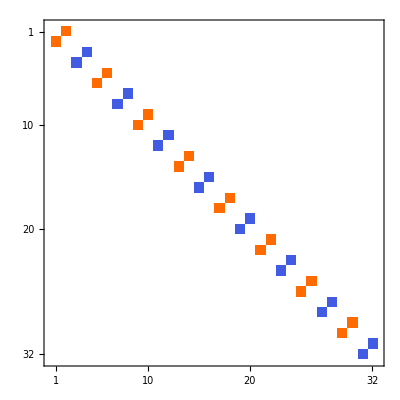
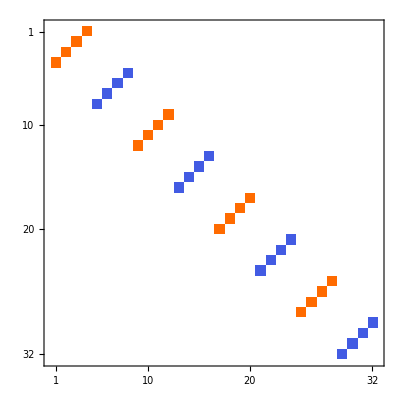
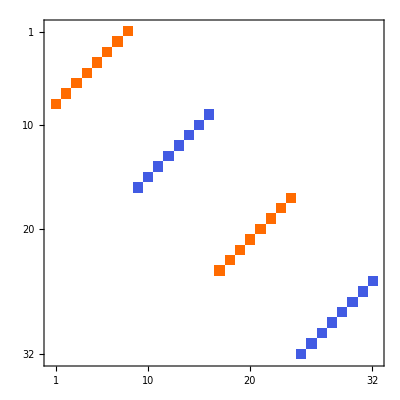
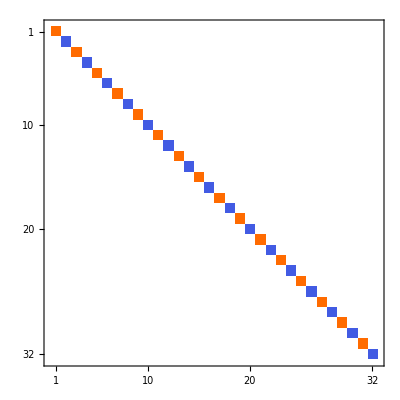
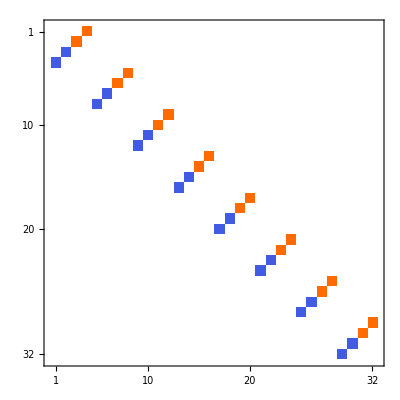
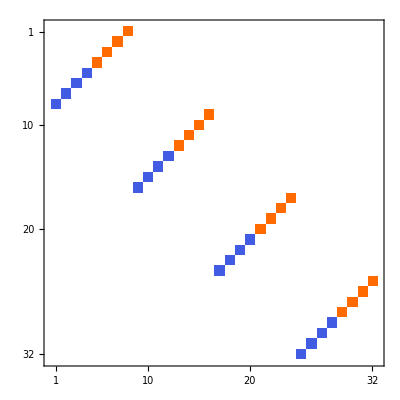
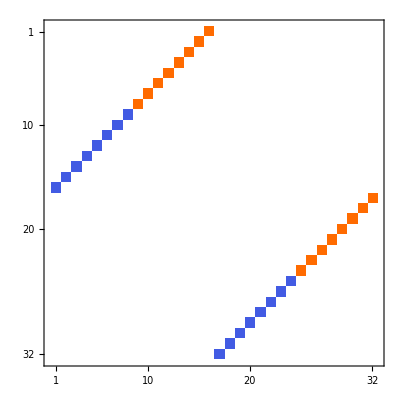
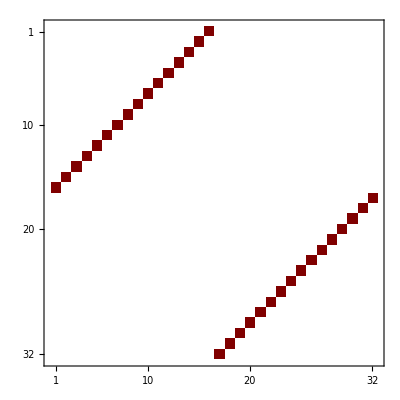
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
MatrixPlot/@(vectors[testAlgebra,1]=gaAlgebraToMatrixRepresentation[testAlgebra])
```

It is easy to see that dark red entries correspond to quaternions (i.𝕖. symbolic entries)

```mathematica
vectors[testAlgebra,1][[8]]
```

gaDefineInput::gaTensorProductAlgebra: gaRunningAlgebra was set to tensor product 1. Input alias of base element was disabled, it only works with Cl[p,q] algebras.

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1020Quaternion,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1020Quaternion,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1020Quaternion,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1020Quaternion,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1020Quaternion,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1020Quaternion,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1020Quaternion,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1020Quaternion,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1020Quaternion,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1020Quaternion,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1020Quaternion,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1020Quaternion,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1020Quaternion,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1020Quaternion,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1020Quaternion,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1020Quaternion,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1020Quaternion},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1020Quaternion,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1020Quaternion,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1020Quaternion,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1020Quaternion,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1020Quaternion,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1020Quaternion,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1020Quaternion,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1020Quaternion,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1020Quaternion,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1020Quaternion,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1020Quaternion,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1020Quaternion,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1020Quaternion,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1020Quaternion,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1020Quaternion,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

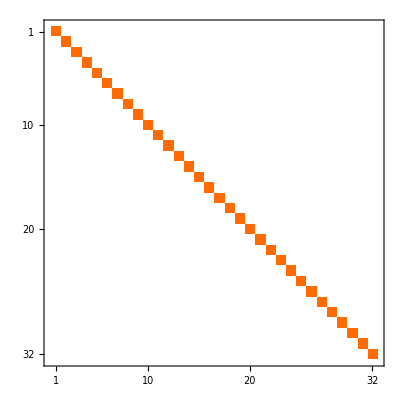
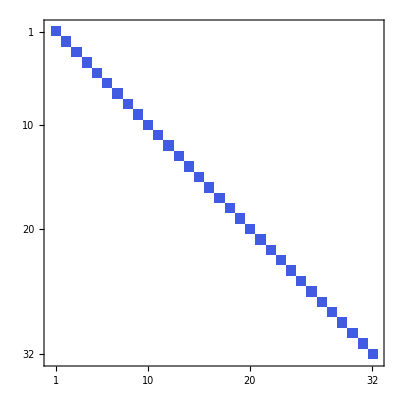
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
MatrixPlot/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

Test the interesting determinat property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

{(x$233183[1]^2+x$233183[2]^2+x$233183[3]^2+x$233183[4]^2-x$233183[5]^2-x$233183[6]^2-x$233183[7]^2-x$233183[8]^2-x$233183[9]^2-x$233183[10]^2-x$233183[11]^2)^16,(x$233183[1]^2+x$233183[2]^2+x$233183[3]^2+x$233183[4]^2-x$233183[5]^2-x$233183[6]^2-x$233183[7]^2-x$233183[8]^2-x$233183[9]^2-x$233183[10]^2-x$233183[11]^2)^16}

#### Cl[5,0], ->ℍ(2)⊕ℍ(2)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[5,0];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

100020200

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=gaAlgebraToMatrixRepresentation[testAlgebra])
```

gaAlgebraToMatrixRepresentation::NoDefaultData: No explicit default representations of elementary algebras for Cl[5,0,0] was given. Will use {{0→Complex,1→Diagonal,1→Antisymmetric,2→Symmetric,0→{Q[1,2]}},Method→TensorProduct} .

{(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0),(0 | 1020Quaternion | 0 | 0
-1020Quaternion | 0 | 0 | 0
0 | 0 | 0 | 1020Quaternion
0 | 0 | -1020Quaternion | 0),(0 | 2020Quaternion | 0 | 0
-2020Quaternion | 0 | 0 | 0
0 | 0 | 0 | 2020Quaternion
0 | 0 | -2020Quaternion | 0),(0 | 12020Quaternion | 0 | 0
-12020Quaternion | 0 | 0 | 0
0 | 0 | 0 | -12020Quaternion
0 | 0 | 12020Quaternion | 0)}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixForm/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)}

Test the interesting determinat property for vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

{(x$235040[1]^2+x$235040[2]^2+x$235040[3]^2+x$235040[4]^2+x$235040[5]^2)^2,(x$235040[1]^2+x$235040[2]^2+x$235040[3]^2+x$235040[4]^2+x$235040[5]^2)^2}

#### Cl[5,1], ->ℍ(4)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[5,1];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 21 was reached. Start picking colors randomly.

020200110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=gaAlgebraToMatrixRepresentation[testAlgebra])
```

gaAlgebraToMatrixRepresentation::NoDefaultData: No explicit default representations of elementary algebras for Cl[5,1,0] was given. Will use {{0→Complex,1→Diagonal,1→Antisymmetric,2→Symmetric,0→{Q[1,2]}},Method→TensorProduct} .

Base vectors of 020200are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[0, 2, 0], Cl[2, 0, 0]],{0, 1}].

Base vectors of 020200110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[0, 2, 0], Cl[2, 0, 0], Cl[1, 1, 0]],{1}].

{(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -1 | 0),(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0),(0 | 0 | 0 | 1020Quaternion
0 | 0 | 1020Quaternion | 0
0 | -1020Quaternion | 0 | 0
-1020Quaternion | 0 | 0 | 0),(0 | 0 | 0 | 2020Quaternion
0 | 0 | 2020Quaternion | 0
0 | -2020Quaternion | 0 | 0
-2020Quaternion | 0 | 0 | 0),(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0)}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixForm/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

gaDefineInput::gaTensorProductAlgebra: gaRunningAlgebra was set to tensor product 0. Input alias of base element was disabled, it only works with Cl[p,q] algebras.

{(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)}

Test the interesting determinat property for  vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

{(x$240452[1]^2+x$240452[2]^2+x$240452[3]^2+x$240452[4]^2+x$240452[5]^2-x$240452[6]^2)^2,(x$240452[1]^2+x$240452[2]^2+x$240452[3]^2+x$240452[4]^2+x$240452[5]^2-x$240452[6]^2)^2}

#### Cl[5,2], ->ℂ(8)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[5,2];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 21 was reached. Start picking colors randomly.

010200110110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=gaAlgebraToMatrixRepresentation[testAlgebra])
```

gaAlgebraToMatrixRepresentation::NoDefaultData: No explicit default representations of elementary algebras for Cl[5,2,0] was given. Will use {{0→Complex,1→Diagonal,1→Antisymmetric,2→Symmetric,0→Pauli[1,2]},Method→TensorProduct} .

Base vectors of 010200are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[0, 1, 0], Cl[2, 0, 0]],{0, 1}].

Base vectors of 010200110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[0, 1, 0], Cl[2, 0, 0], Cl[1, 1, 0]],{0, 1}].

Base vectors of 010200110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[0, 1, 0], Cl[2, 0, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{1}].

{(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ
0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0
0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0
0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0
0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0
-ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixForm/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

gaDefineInput::gaTensorProductAlgebra: gaRunningAlgebra was set to tensor product 0. Input alias of base element was disabled, it only works with Cl[p,q] algebras.

{(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)}

Test the interesting determinat property for vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

{(x$245885[1]^2+x$245885[2]^2+x$245885[3]^2+x$245885[4]^2+x$245885[5]^2-x$245885[6]^2-x$245885[7]^2)^4,(x$245885[1]^2+x$245885[2]^2+x$245885[3]^2+x$245885[4]^2+x$245885[5]^2-x$245885[6]^2-x$245885[7]^2)^4}

#### Cl[5,3], ->ℝ(16)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[5,3];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 21 was reached. Start picking colors randomly.

200110110110

Base vector matrix representations using default settings

gaAlgebraToMatrixRepresentation::NoDefaultData: No explicit default representations of elementary algebras for Cl[5,3,0] was given. Will use {{1→Diagonal,0→Antisymmetric,1→Antisymmetric,2→IPauli[3,1],0→{Q[1,2]}},Method→{TensorProduct,QuaternionIsomorphismRules→True}} .

Base vectors of 200110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[2, 0, 0], Cl[1, 1, 0]],{0, 1}].

Base vectors of 200110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[2, 0, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{0, 1}].

Base vectors of 200110110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[2, 0, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{1}].

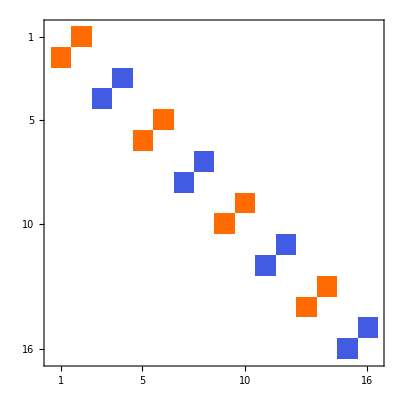
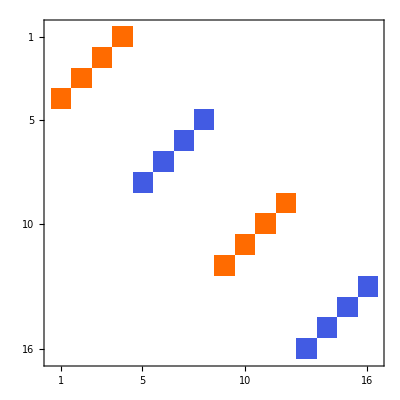
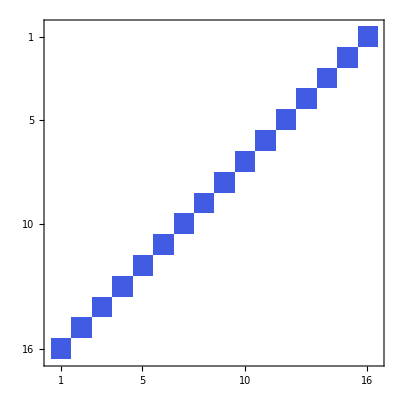
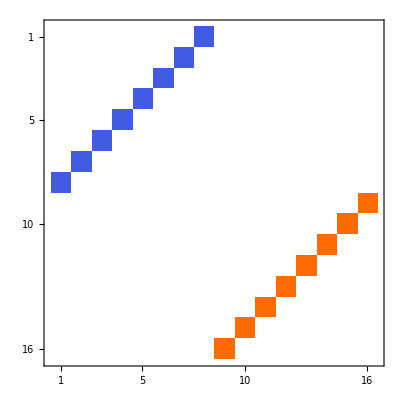
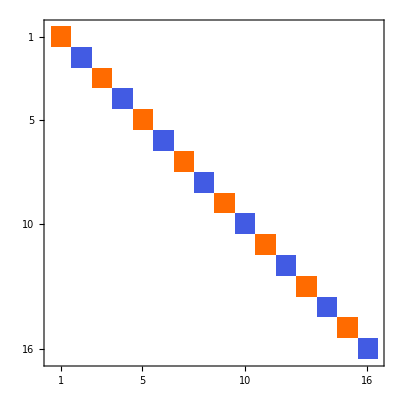
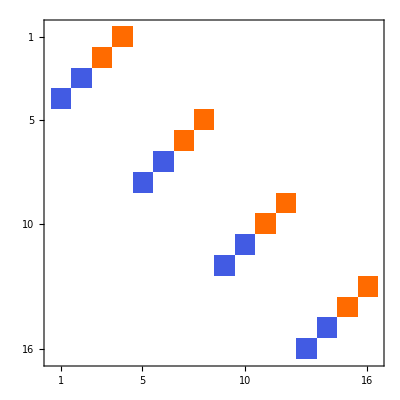
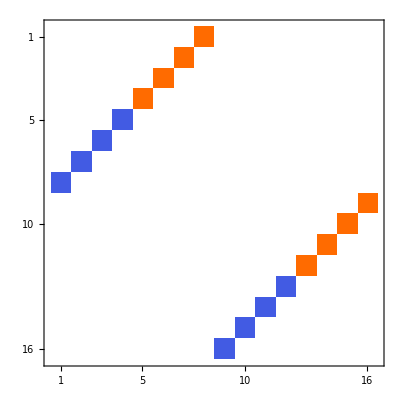
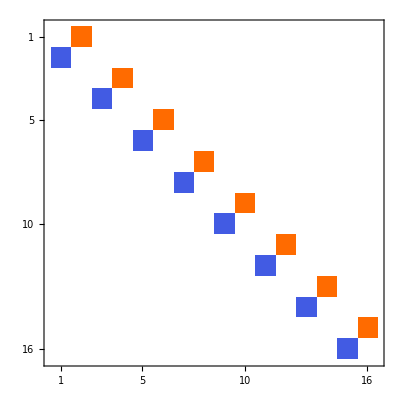

```mathematica
MatrixPlot/@(vectors[testAlgebra,1]=gaAlgebraToMatrixRepresentation[testAlgebra])
```

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixPlot/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

gaDefineInput::gaTensorProductAlgebra: gaRunningAlgebra was set to tensor product 2. Input alias of base element was disabled, it only works with Cl[p,q] algebras.

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Test the interesting determinat property for vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

{(x$252310[1]^2+x$252310[2]^2+x$252310[3]^2+x$252310[4]^2+x$252310[5]^2-x$252310[6]^2-x$252310[7]^2-x$252310[8]^2)^8,(x$252310[1]^2+x$252310[2]^2+x$252310[3]^2+x$252310[4]^2+x$252310[5]^2-x$252310[6]^2-x$252310[7]^2-x$252310[8]^2)^8}

#### Cl[5,4], ->ℝ(16)⊕ℝ(16)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[5,4];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 21 was reached. Start picking colors randomly.

100110110110110

Base vector matrix representations using default settings

```mathematica
MatrixPlot/@(vectors[testAlgebra,1]=gaAlgebraToMatrixRepresentation[testAlgebra])
```

gaAlgebraToMatrixRepresentation::NoDefaultData: No explicit default representations of elementary algebras for Cl[5,4,0] was given. Will use {{1→Diagonal,0→Antisymmetric,1→Antisymmetric,2→IPauli[3,1],0→{Q[1,2]}},Method→{TensorProduct,QuaternionIsomorphismRules→True}} .

Base vectors of 100110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[1, 0, 0], Cl[1, 1, 0]],{0, 1}].

Base vectors of 100110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[1, 0, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{0, 1}].

Base vectors of 100110110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[1, 0, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{0, 1}].

Base vectors of 100110110110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[1, 0, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{1}].

gaAlgebraToMatrixRepresentation::smaller: Tensor product decomposition 1 contains Cl[1,0] algebra. Smaller (complex) representation matrices can be obtained using Method ->{"TensorProduct",BaseVectorAlgebra→4,TargetMatrices→Reals}. The smaller matrices realizes HOMOMORPHISM of the algebra (not an isomorphism).

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixPlot/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

gaDefineInput::gaTensorProductAlgebra: gaRunningAlgebra was set to tensor product 1. Input alias of base element was disabled, it only works with Cl[p,q] algebras.

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Test the interesting determinat property for vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

{(x$260667[1]^2+x$260667[2]^2+x$260667[3]^2+x$260667[4]^2+x$260667[5]^2-x$260667[6]^2-x$260667[7]^2-x$260667[8]^2-x$260667[9]^2)^16,(x$260667[1]^2+x$260667[2]^2+x$260667[3]^2+x$260667[4]^2+x$260667[5]^2-x$260667[6]^2-x$260667[7]^2-x$260667[8]^2-x$260667[9]^2)^16}

#### Cl[5,5], ->ℝ(32)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[5,5];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 21 was reached. Start picking colors randomly.

110110110110110

Base vector matrix representations using default settings

```mathematica
MatrixPlot/@(vectors[testAlgebra,1]=gaAlgebraToMatrixRepresentation[testAlgebra])
```

gaAlgebraToMatrixRepresentation::NoDefaultData: No explicit default representations of elementary algebras for Cl[5,5,0] was given. Will use {{1→Diagonal,0→Antisymmetric,1→Antisymmetric,2→IPauli[3,1],0→{Q[1,2]}},Method→{TensorProduct,QuaternionIsomorphismRules→True}} .

Base vectors of 110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[1, 1, 0], Cl[1, 1, 0]],{0, 1}].

Base vectors of 110110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{0, 1}].

Base vectors of 110110110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{0, 1}].

Base vectors of 110110110110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{1}].

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Squares of sparse matrices can be calculated using  Dot[ ].

```mathematica
MatrixPlot/@(Dot[#,#]&/@(SparseArray/@vectors[testAlgebra,1]))
```

gaDefineInput::gaTensorProductAlgebra: gaRunningAlgebra was set to tensor product 1. Input alias of base element was disabled, it only works with Cl[p,q] algebras.

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Test the interesting determinat property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

{(x$267411[1]^2+x$267411[2]^2+x$267411[3]^2+x$267411[4]^2+x$267411[5]^2-x$267411[6]^2-x$267411[7]^2-x$267411[8]^2-x$267411[9]^2-x$267411[10]^2)^16,(x$267411[1]^2+x$267411[2]^2+x$267411[3]^2+x$267411[4]^2+x$267411[5]^2-x$267411[6]^2-x$267411[7]^2-x$267411[8]^2-x$267411[9]^2-x$267411[10]^2)^16}

#### Cl[5,6], ->ℂ(32)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[5,6];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 21 was reached. Start picking colors randomly.

010110110110110110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=gaAlgebraToMatrixRepresentation[testAlgebra])
```

gaAlgebraToMatrixRepresentation::NoDefaultData: No explicit default representations of elementary algebras for Cl[5,6,0] was given. Will use {{0→Complex,1→Diagonal,1→Antisymmetric,2→Symmetric,0→Pauli[1,2]},Method→TensorProduct} .

Base vectors of 010110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[0, 1, 0], Cl[1, 1, 0]],{0, 1}].

Base vectors of 010110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[0, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{0, 1}].

Base vectors of 010110110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[0, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{0, 1}].

Base vectors of 010110110110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[0, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{0, 1}].

Base vectors of 010110110110110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[0, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{1}].

{(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixForm/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

gaDefineInput::gaTensorProductAlgebra: gaRunningAlgebra was set to tensor product 0. Input alias of base element was disabled, it only works with Cl[p,q] algebras.

{(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)}

Test the interesting determinat property. Calculation of matrix determinant  now takes too much memory, calculate only Clifford rezult

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False,onlyClifford->True]
```

(-x$272976[1]^2-x$272976[2]^2-x$272976[3]^2-x$272976[4]^2-x$272976[5]^2+x$272976[6]^2+x$272976[7]^2+x$272976[8]^2+x$272976[9]^2+x$272976[10]^2+x$272976[11]^2)^16

#### Cl[5,7], ->ℍ(32)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[5,7];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 21 was reached. Start picking colors randomly.

020110110110110110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=gaAlgebraToMatrixRepresentation[testAlgebra])
```

gaAlgebraToMatrixRepresentation::NoDefaultData: No explicit default representations of elementary algebras for Cl[5,7,0] was given. Will use {{0→Complex,1→Diagonal,1→Antisymmetric,2→Symmetric,0→{Q[1,2]}},Method→TensorProduct} .

Base vectors of 020110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[0, 2, 0], Cl[1, 1, 0]],{0, 1}].

Base vectors of 020110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[0, 2, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{0, 1}].

Base vectors of 020110110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[0, 2, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{0, 1}].

Base vectors of 020110110110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[0, 2, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{0, 1}].

Base vectors of 020110110110110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[0, 2, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{1}].

{(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixForm/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

gaDefineInput::gaTensorProductAlgebra: gaRunningAlgebra was set to tensor product 0. Input alias of base element was disabled, it only works with Cl[p,q] algebras.

{(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)}

Test the interesting determinat property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False,onlyClifford->True]
```

(-x$278653[1]^2-x$278653[2]^2-x$278653[3]^2-x$278653[4]^2-x$278653[5]^2+x$278653[6]^2+x$278653[7]^2+x$278653[8]^2+x$278653[9]^2+x$278653[10]^2+x$278653[11]^2+x$278653[12]^2)^16

#### Cl[6,0], ->ℍ(4)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[6,0];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 21 was reached. Start picking colors randomly.

200020200

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=gaAlgebraToMatrixRepresentation[testAlgebra])
```

gaAlgebraToMatrixRepresentation::NoDefaultData: No explicit default representations of elementary algebras for Cl[6,0,0] was given. Will use {{0→Complex,1→Diagonal,1→Antisymmetric,2→Symmetric,0→{Q[1,2]}},Method→TensorProduct} .

Base vectors of 200020are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[2, 0, 0], Cl[0, 2, 0]],{0, 1}].

Base vectors of 200020200are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[2, 0, 0], Cl[0, 2, 0], Cl[2, 0, 0]],{1}].

{(0 | 1020Quaternion | 0 | 0
-1020Quaternion | 0 | 0 | 0
0 | 0 | 0 | 1020Quaternion
0 | 0 | -1020Quaternion | 0),(0 | 2020Quaternion | 0 | 0
-2020Quaternion | 0 | 0 | 0
0 | 0 | 0 | 2020Quaternion
0 | 0 | -2020Quaternion | 0),(0 | 12020Quaternion | 0 | 0
-12020Quaternion | 0 | 0 | 0
0 | 0 | 0 | -12020Quaternion
0 | 0 | 12020Quaternion | 0),(0 | 0 | 0 | 12020Quaternion
0 | 0 | -12020Quaternion | 0
0 | 12020Quaternion | 0 | 0
-12020Quaternion | 0 | 0 | 0),(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0)}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixForm/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

gaDefineInput::gaTensorProductAlgebra: gaRunningAlgebra was set to tensor product 2. Input alias of base element was disabled, it only works with Cl[p,q] algebras.

{(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)}

Test the interesting determinat property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

{(x$284067[1]^2+x$284067[2]^2+x$284067[3]^2+x$284067[4]^2+x$284067[5]^2+x$284067[6]^2)^2,(x$284067[1]^2+x$284067[2]^2+x$284067[3]^2+x$284067[4]^2+x$284067[5]^2+x$284067[6]^2)^2}

#### Cl[6,1], ->ℍ(4)⊕ℍ(4)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[6,1];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 21 was reached. Start picking colors randomly.

100020200110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=gaAlgebraToMatrixRepresentation[testAlgebra])
```

gaAlgebraToMatrixRepresentation::NoDefaultData: No explicit default representations of elementary algebras for Cl[6,1,0] was given. Will use {{0→Complex,1→Diagonal,1→Antisymmetric,2→Symmetric,0→{Q[1,2]}},Method→TensorProduct} .

Base vectors of 100020are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[1, 0, 0], Cl[0, 2, 0]],{0, 1}].

Base vectors of 100020200are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[1, 0, 0], Cl[0, 2, 0], Cl[2, 0, 0]],{0, 1}].

Base vectors of 100020200110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[1, 0, 0], Cl[0, 2, 0], Cl[2, 0, 0], Cl[1, 1, 0]],{1}].

{(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0),(0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0
0 | -1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
-1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0
0 | 0 | 0 | 0 | 0 | -1020Quaternion | 0 | 0
0 | 0 | 0 | 0 | -1020Quaternion | 0 | 0 | 0),(0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0
0 | -2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
-2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0
0 | 0 | 0 | 0 | 0 | -2020Quaternion | 0 | 0
0 | 0 | 0 | 0 | -2020Quaternion | 0 | 0 | 0),(0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0
0 | -12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
-12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion | 0
0 | 0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0
0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixForm/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

gaDefineInput::gaTensorProductAlgebra: gaRunningAlgebra was set to tensor product 1. Input alias of base element was disabled, it only works with Cl[p,q] algebras.

{(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)}

Test the interesting determinat property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

{(x$289518[1]^2+x$289518[2]^2+x$289518[3]^2+x$289518[4]^2+x$289518[5]^2+x$289518[6]^2-x$289518[7]^2)^4,(x$289518[1]^2+x$289518[2]^2+x$289518[3]^2+x$289518[4]^2+x$289518[5]^2+x$289518[6]^2-x$289518[7]^2)^4}

#### Cl[6,2], ->ℍ(8)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[6,2];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 21 was reached. Start picking colors randomly.

020200110110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=gaAlgebraToMatrixRepresentation[testAlgebra])
```

gaAlgebraToMatrixRepresentation::NoDefaultData: No explicit default representations of elementary algebras for Cl[6,2,0] was given. Will use {{0→Complex,1→Diagonal,1→Antisymmetric,2→Symmetric,0→{Q[1,2]}},Method→TensorProduct} .

Base vectors of 020200are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[0, 2, 0], Cl[2, 0, 0]],{0, 1}].

Base vectors of 020200110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[0, 2, 0], Cl[2, 0, 0], Cl[1, 1, 0]],{0, 1}].

Base vectors of 020200110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[0, 2, 0], Cl[2, 0, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{1}].

{(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0
0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0
0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0
0 | 0 | 0 | -1020Quaternion | 0 | 0 | 0 | 0
0 | 0 | -1020Quaternion | 0 | 0 | 0 | 0 | 0
0 | -1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
-1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0
0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0
0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0
0 | 0 | 0 | -2020Quaternion | 0 | 0 | 0 | 0
0 | 0 | -2020Quaternion | 0 | 0 | 0 | 0 | 0
0 | -2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
-2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixForm/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

gaDefineInput::gaTensorProductAlgebra: gaRunningAlgebra was set to tensor product 0. Input alias of base element was disabled, it only works with Cl[p,q] algebras.

{(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)}

Test the interesting determinat property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

{(x$295002[1]^2+x$295002[2]^2+x$295002[3]^2+x$295002[4]^2+x$295002[5]^2+x$295002[6]^2-x$295002[7]^2-x$295002[8]^2)^4,(x$295002[1]^2+x$295002[2]^2+x$295002[3]^2+x$295002[4]^2+x$295002[5]^2+x$295002[6]^2-x$295002[7]^2-x$295002[8]^2)^4}

#### Cl[6,3], ->ℂ(16)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[6,3];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 21 was reached. Start picking colors randomly.

010200110110110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=gaAlgebraToMatrixRepresentation[testAlgebra])
```

gaAlgebraToMatrixRepresentation::NoDefaultData: No explicit default representations of elementary algebras for Cl[6,3,0] was given. Will use {{0→Complex,1→Diagonal,1→Antisymmetric,2→Symmetric,0→Pauli[1,2]},Method→TensorProduct} .

Base vectors of 010200are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[0, 1, 0], Cl[2, 0, 0]],{0, 1}].

Base vectors of 010200110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[0, 1, 0], Cl[2, 0, 0], Cl[1, 1, 0]],{0, 1}].

Base vectors of 010200110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[0, 1, 0], Cl[2, 0, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{0, 1}].

Base vectors of 010200110110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[0, 1, 0], Cl[2, 0, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{1}].

{(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixForm/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

gaDefineInput::gaTensorProductAlgebra: gaRunningAlgebra was set to tensor product 0. Input alias of base element was disabled, it only works with Cl[p,q] algebras.

{(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)}

Test the interesting determinat property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

{(x$300500[1]^2+x$300500[2]^2+x$300500[3]^2+x$300500[4]^2+x$300500[5]^2+x$300500[6]^2-x$300500[7]^2-x$300500[8]^2-x$300500[9]^2)^8,(x$300500[1]^2+x$300500[2]^2+x$300500[3]^2+x$300500[4]^2+x$300500[5]^2+x$300500[6]^2-x$300500[7]^2-x$300500[8]^2-x$300500[9]^2)^8}

#### Cl[6,4], ->ℝ(32)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[6,4];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 21 was reached. Start picking colors randomly.

200110110110110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=gaAlgebraToMatrixRepresentation[testAlgebra])
```

gaAlgebraToMatrixRepresentation::NoDefaultData: No explicit default representations of elementary algebras for Cl[6,4,0] was given. Will use {{1→Diagonal,0→Antisymmetric,1→Antisymmetric,2→IPauli[3,1],0→{Q[1,2]}},Method→{TensorProduct,QuaternionIsomorphismRules→True}} .

Base vectors of 200110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[2, 0, 0], Cl[1, 1, 0]],{0, 1}].

Base vectors of 200110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[2, 0, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{0, 1}].

Base vectors of 200110110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[2, 0, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{0, 1}].

Base vectors of 200110110110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[2, 0, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{1}].

{(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixForm/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

gaDefineInput::gaTensorProductAlgebra: gaRunningAlgebra was set to tensor product 2. Input alias of base element was disabled, it only works with Cl[p,q] algebras.

{(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)}

Test the interesting determinat property. Calculation of matrix determinant  now takes too much memory, calculate only Clifford rezult

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False,onlyClifford->True]
```

(-x$306024[1]^2-x$306024[2]^2-x$306024[3]^2-x$306024[4]^2-x$306024[5]^2-x$306024[6]^2+x$306024[7]^2+x$306024[8]^2+x$306024[9]^2+x$306024[10]^2)^16

#### Cl[6,5], ->ℝ(32)⊕ℝ(32)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[6,5];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 21 was reached. Start picking colors randomly.

100110110110110110

Base vector matrix representations using default settings. Due to large matrix size we just plot matrix shapes (orange poins are +1, blue represents -1)

```mathematica
MatrixPlot/@(vectors[testAlgebra,1]=gaAlgebraToMatrixRepresentation[testAlgebra])
```

gaAlgebraToMatrixRepresentation::NoDefaultData: No explicit default representations of elementary algebras for Cl[6,5,0] was given. Will use {{1→Diagonal,0→Antisymmetric,1→Antisymmetric,2→IPauli[3,1],0→{Q[1,2]}},Method→{TensorProduct,QuaternionIsomorphismRules→True}} .

Base vectors of 100110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[1, 0, 0], Cl[1, 1, 0]],{0, 1}].

Base vectors of 100110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[1, 0, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{0, 1}].

Base vectors of 100110110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[1, 0, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{0, 1}].

Base vectors of 100110110110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[1, 0, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{0, 1}].

Base vectors of 100110110110110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[1, 0, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{1}].

gaAlgebraToMatrixRepresentation::smaller: Tensor product decomposition 1 contains Cl[1,0] algebra. Smaller (complex) representation matrices can be obtained using Method ->{"TensorProduct",BaseVectorAlgebra→5,TargetMatrices→Reals}. The smaller matrices realizes HOMOMORPHISM of the algebra (not an isomorphism).

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixPlot/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

gaDefineInput::gaTensorProductAlgebra: gaRunningAlgebra was set to tensor product 1. Input alias of base element was disabled, it only works with Cl[p,q] algebras.

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Test the interesting determinat property. Calculation of matrix determinant  now takes too much memory, calculate only Clifford rezult

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False,onlyClifford->True]
```

(-x$314705[1]^2-x$314705[2]^2-x$314705[3]^2-x$314705[4]^2-x$314705[5]^2-x$314705[6]^2+x$314705[7]^2+x$314705[8]^2+x$314705[9]^2+x$314705[10]^2+x$314705[11]^2)^32

#### Cl[6,6], ->ℝ(64)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[6,6];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 21 was reached. Start picking colors randomly.

110110110110110110

Base vector matrix representations using default settings. Due to large matrix size we just plot matrix shapes (orange poins are +1, blue represents -1)

```mathematica
MatrixPlot/@(vectors[testAlgebra,1]=gaAlgebraToMatrixRepresentation[testAlgebra])
```

gaAlgebraToMatrixRepresentation::NoDefaultData: No explicit default representations of elementary algebras for Cl[6,6,0] was given. Will use {{1→Diagonal,0→Antisymmetric,1→Antisymmetric,2→IPauli[3,1],0→{Q[1,2]}},Method→{TensorProduct,QuaternionIsomorphismRules→True}} .

Base vectors of 110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[1, 1, 0], Cl[1, 1, 0]],{0, 1}].

Base vectors of 110110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{0, 1}].

Base vectors of 110110110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{0, 1}].

Base vectors of 110110110110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{0, 1}].

Base vectors of 110110110110110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{1}].

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixPlot/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

gaDefineInput::gaTensorProductAlgebra: gaRunningAlgebra was set to tensor product 1. Input alias of base element was disabled, it only works with Cl[p,q] algebras.

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Test the interesting determinat property. Calculation of matrix determinant  now takes too much memory, calculate only Clifford rezult

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False,onlyClifford->True]
```

(-x$321774[1]^2-x$321774[2]^2-x$321774[3]^2-x$321774[4]^2-x$321774[5]^2-x$321774[6]^2+x$321774[7]^2+x$321774[8]^2+x$321774[9]^2+x$321774[10]^2+x$321774[11]^2+x$321774[12]^2)^32

#### Cl[6,7], ->ℂ(64)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[6,7];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 21 was reached. Start picking colors randomly.

010110110110110110110

Base vector matrix representations using default settings. Due to large matrix size we just plot matrix shapes (orange poins are +1, blue represents -1)

```mathematica
MatrixPlot/@(vectors[testAlgebra,1]=gaAlgebraToMatrixRepresentation[testAlgebra])
```

gaAlgebraToMatrixRepresentation::NoDefaultData: No explicit default representations of elementary algebras for Cl[6,7,0] was given. Will use {{0→Complex,1→Diagonal,1→Antisymmetric,2→Symmetric,0→Pauli[1,2]},Method→TensorProduct} .

Base vectors of 010110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[0, 1, 0], Cl[1, 1, 0]],{0, 1}].

Base vectors of 010110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[0, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{0, 1}].

Base vectors of 010110110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[0, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{0, 1}].

Base vectors of 010110110110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[0, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{0, 1}].

Base vectors of 010110110110110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[0, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{0, 1}].

Base vectors of 010110110110110110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[0, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{1}].

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixPlot/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

gaDefineInput::gaTensorProductAlgebra: gaRunningAlgebra was set to tensor product 0. Input alias of base element was disabled, it only works with Cl[p,q] algebras.

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Test the interesting determinat property. Calculation of matrix determinant  now takes too much memory, calculate only Clifford rezult

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False,onlyClifford->True]
```

(-x$329014[1]^2-x$329014[2]^2-x$329014[3]^2-x$329014[4]^2-x$329014[5]^2-x$329014[6]^2+x$329014[7]^2+x$329014[8]^2+x$329014[9]^2+x$329014[10]^2+x$329014[11]^2+x$329014[12]^2+x$329014[13]^2)^32

#### Cl[7,0], ->ℂ(8)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[7,0];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 21 was reached. Start picking colors randomly.

010200020200

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=gaAlgebraToMatrixRepresentation[testAlgebra])
```

gaAlgebraToMatrixRepresentation::NoDefaultData: No explicit default representations of elementary algebras for Cl[7,0,0] was given. Will use {{0→Complex,1→Diagonal,1→Antisymmetric,2→Symmetric,0→Pauli[1,2]},Method→TensorProduct} .

Base vectors of 010200are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[0, 1, 0], Cl[2, 0, 0]],{0, 1}].

Base vectors of 010200020are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[0, 1, 0], Cl[2, 0, 0], Cl[0, 2, 0]],{0, 1}].

Base vectors of 010200020200are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[0, 1, 0], Cl[2, 0, 0], Cl[0, 2, 0], Cl[2, 0, 0]],{1}].

{(0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0
-ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0
0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0
0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ
0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0),(0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0
0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0
-ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ
0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0
0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ
0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0
0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0
0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0
0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0
0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0
-ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixForm/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

gaDefineInput::gaTensorProductAlgebra: gaRunningAlgebra was set to tensor product 0. Input alias of base element was disabled, it only works with Cl[p,q] algebras.

{(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)}

Test the interesting determinat property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

{(x$334439[1]^2+x$334439[2]^2+x$334439[3]^2+x$334439[4]^2+x$334439[5]^2+x$334439[6]^2+x$334439[7]^2)^4,(x$334439[1]^2+x$334439[2]^2+x$334439[3]^2+x$334439[4]^2+x$334439[5]^2+x$334439[6]^2+x$334439[7]^2)^4}

#### Cl[7,1], ->ℍ(8)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[7,1];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 21 was reached. Start picking colors randomly.

200020200110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=gaAlgebraToMatrixRepresentation[testAlgebra])
```

gaAlgebraToMatrixRepresentation::NoDefaultData: No explicit default representations of elementary algebras for Cl[7,1,0] was given. Will use {{0→Complex,1→Diagonal,1→Antisymmetric,2→Symmetric,0→{Q[1,2]}},Method→TensorProduct} .

Base vectors of 200020are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[2, 0, 0], Cl[0, 2, 0]],{0, 1}].

Base vectors of 200020200are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[2, 0, 0], Cl[0, 2, 0], Cl[2, 0, 0]],{0, 1}].

Base vectors of 200020200110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[2, 0, 0], Cl[0, 2, 0], Cl[2, 0, 0], Cl[1, 1, 0]],{1}].

{(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0),(0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0
0 | -1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
-1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0
0 | 0 | 0 | 0 | 0 | -1020Quaternion | 0 | 0
0 | 0 | 0 | 0 | -1020Quaternion | 0 | 0 | 0),(0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0
0 | -2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
-2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0
0 | 0 | 0 | 0 | 0 | -2020Quaternion | 0 | 0
0 | 0 | 0 | 0 | -2020Quaternion | 0 | 0 | 0),(0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0
0 | -12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
-12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion | 0
0 | 0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0
0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 12020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | 12020Quaternion | 0
0 | 0 | 0 | 0 | 0 | -12020Quaternion | 0 | 0
0 | 0 | 0 | 0 | -12020Quaternion | 0 | 0 | 0
0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0
0 | -12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
-12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixForm/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

gaDefineInput::gaTensorProductAlgebra: gaRunningAlgebra was set to tensor product 2. Input alias of base element was disabled, it only works with Cl[p,q] algebras.

{(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)}

Test the interesting determinat property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

{(x$339909[1]^2+x$339909[2]^2+x$339909[3]^2+x$339909[4]^2+x$339909[5]^2+x$339909[6]^2+x$339909[7]^2-x$339909[8]^2)^4,(x$339909[1]^2+x$339909[2]^2+x$339909[3]^2+x$339909[4]^2+x$339909[5]^2+x$339909[6]^2+x$339909[7]^2-x$339909[8]^2)^4}

#### Cl[7,2], ->ℍ(8)⊕ℍ(8)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[7,2];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 21 was reached. Start picking colors randomly.

100020200110110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=gaAlgebraToMatrixRepresentation[testAlgebra])
```

gaAlgebraToMatrixRepresentation::NoDefaultData: No explicit default representations of elementary algebras for Cl[7,2,0] was given. Will use {{0→Complex,1→Diagonal,1→Antisymmetric,2→Symmetric,0→{Q[1,2]}},Method→TensorProduct} .

Base vectors of 100020are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[1, 0, 0], Cl[0, 2, 0]],{0, 1}].

Base vectors of 100020200are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[1, 0, 0], Cl[0, 2, 0], Cl[2, 0, 0]],{0, 1}].

Base vectors of 100020200110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[1, 0, 0], Cl[0, 2, 0], Cl[2, 0, 0], Cl[1, 1, 0]],{0, 1}].

{(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1020Quaternion | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2020Quaternion | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0)}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixPlot/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Test the interesting determinat property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

{(x$39807[1]^2+x$39807[2]^2+x$39807[3]^2+x$39807[4]^2+x$39807[5]^2+x$39807[6]^2+x$39807[7]^2-x$39807[8]^2-x$39807[9]^2)^8,(x$39807[1]^2+x$39807[2]^2+x$39807[3]^2+x$39807[4]^2+x$39807[5]^2+x$39807[6]^2+x$39807[7]^2-x$39807[8]^2-x$39807[9]^2)^8}

#### Cl[7,3], ->ℍ(16)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[7,3];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 21 was reached. Start picking colors randomly.

020200110110110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=gaAlgebraToMatrixRepresentation[testAlgebra])
```

gaAlgebraToMatrixRepresentation::NoDefaultData: No explicit default representations of elementary algebras for Cl[7,3,0] was given. Will use {{0→Complex,1→Diagonal,1→Antisymmetric,2→Symmetric,0→{Q[1,2]}},Method→TensorProduct} .

Base vectors of 020200are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[0, 2, 0], Cl[2, 0, 0]],{0, 1}].

Base vectors of 020200110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[0, 2, 0], Cl[2, 0, 0], Cl[1, 1, 0]],{0, 1}].

Base vectors of 020200110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[0, 2, 0], Cl[2, 0, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{0, 1}].

Base vectors of 020200110110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[0, 2, 0], Cl[2, 0, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{1}].

{(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixPlot/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

gaDefineInput::gaTensorProductAlgebra: gaRunningAlgebra was set to tensor product 0. Input alias of base element was disabled, it only works with Cl[p,q] algebras.

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Test the interesting determinat property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

{(x$352175[1]^2+x$352175[2]^2+x$352175[3]^2+x$352175[4]^2+x$352175[5]^2+x$352175[6]^2+x$352175[7]^2-x$352175[8]^2-x$352175[9]^2-x$352175[10]^2)^8,(x$352175[1]^2+x$352175[2]^2+x$352175[3]^2+x$352175[4]^2+x$352175[5]^2+x$352175[6]^2+x$352175[7]^2-x$352175[8]^2-x$352175[9]^2-x$352175[10]^2)^8}

#### Cl[7,4], ->ℂ(32)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[7,4];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 21 was reached. Start picking colors randomly.

010200110110110110

Base vector matrix representations using default settings. Due to large matrix size we just plot matrix shapes (orange poins are +1, blue represents -1)

```mathematica
MatrixPlot/@(vectors[testAlgebra,1]=gaAlgebraToMatrixRepresentation[testAlgebra])
```

gaAlgebraToMatrixRepresentation::NoDefaultData: No explicit default representations of elementary algebras for Cl[7,4,0] was given. Will use {{0→Complex,1→Diagonal,1→Antisymmetric,2→Symmetric,0→Pauli[1,2]},Method→TensorProduct} .

Base vectors of 010200are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[0, 1, 0], Cl[2, 0, 0]],{0, 1}].

Base vectors of 010200110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[0, 1, 0], Cl[2, 0, 0], Cl[1, 1, 0]],{0, 1}].

Base vectors of 010200110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[0, 1, 0], Cl[2, 0, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{0, 1}].

Base vectors of 010200110110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[0, 1, 0], Cl[2, 0, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{0, 1}].

Base vectors of 010200110110110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[0, 1, 0], Cl[2, 0, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{1}].

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

The empty “matrix” has purely complex entries:

```mathematica
vectors[testAlgebra,1][[6]]
```

gaDefineInput::gaTensorProductAlgebra: gaRunningAlgebra was set to tensor product 0. Input alias of base element was disabled, it only works with Cl[p,q] algebras.

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,-ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,-ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,-ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,-ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,-ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,-ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,-ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,-ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,-ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,-ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixPlot/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Test the interesting determinat property. Calculation of matrix determinant  now takes too much memory, calculate only Clifford rezult

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False,onlyClifford->True]
```

(-x$359100[1]^2-x$359100[2]^2-x$359100[3]^2-x$359100[4]^2-x$359100[5]^2-x$359100[6]^2-x$359100[7]^2+x$359100[8]^2+x$359100[9]^2+x$359100[10]^2+x$359100[11]^2)^16

#### Cl[7,5], ->ℝ(64)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[7,5];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 21 was reached. Start picking colors randomly.

200110110110110110

Base vector matrix representations using default settings. Due to large matrix size we just plot matrix shapes (orange poins are +1, blue represents -1)

```mathematica
MatrixPlot/@(vectors[testAlgebra,1]=gaAlgebraToMatrixRepresentation[testAlgebra])
```

gaAlgebraToMatrixRepresentation::NoDefaultData: No explicit default representations of elementary algebras for Cl[7,5,0] was given. Will use {{1→Diagonal,0→Antisymmetric,1→Antisymmetric,2→IPauli[3,1],0→{Q[1,2]}},Method→{TensorProduct,QuaternionIsomorphismRules→True}} .

Base vectors of 200110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[2, 0, 0], Cl[1, 1, 0]],{0, 1}].

Base vectors of 200110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[2, 0, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{0, 1}].

Base vectors of 200110110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[2, 0, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{0, 1}].

Base vectors of 200110110110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[2, 0, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{0, 1}].

Base vectors of 200110110110110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[2, 0, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{1}].

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixPlot/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

gaDefineInput::gaTensorProductAlgebra: gaRunningAlgebra was set to tensor product 2. Input alias of base element was disabled, it only works with Cl[p,q] algebras.

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Test the interesting determinat property. Calculation of matrix determinant  now takes too much memory, calculate only Clifford rezult

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False,onlyClifford->True]
```

(-x$366173[1]^2-x$366173[2]^2-x$366173[3]^2-x$366173[4]^2-x$366173[5]^2-x$366173[6]^2-x$366173[7]^2+x$366173[8]^2+x$366173[9]^2+x$366173[10]^2+x$366173[11]^2+x$366173[12]^2)^32

#### Cl[7,6], ->ℝ(64)⊕ℝ(64)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[7,6];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 21 was reached. Start picking colors randomly.

100110110110110110110

Base vector matrix representations using default settings. Due to large matrix size we just plot matrix shapes (orange poins are +1, blue represents -1)

```mathematica
MatrixPlot/@(vectors[testAlgebra,1]=gaAlgebraToMatrixRepresentation[testAlgebra])
```

gaAlgebraToMatrixRepresentation::NoDefaultData: No explicit default representations of elementary algebras for Cl[7,6,0] was given. Will use {{1→Diagonal,0→Antisymmetric,1→Antisymmetric,2→IPauli[3,1],0→{Q[1,2]}},Method→{TensorProduct,QuaternionIsomorphismRules→True}} .

Base vectors of 100110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[1, 0, 0], Cl[1, 1, 0]],{0, 1}].

Base vectors of 100110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[1, 0, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{0, 1}].

Base vectors of 100110110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[1, 0, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{0, 1}].

gaAlgebraToMatrixRepresentation::smaller: Tensor product decomposition 1 contains Cl[1,0] algebra. Smaller (complex) representation matrices can be obtained using Method ->{"TensorProduct",BaseVectorAlgebra→Cl[6,7,0],TargetMatrices→Reals}. The smaller matrices realizes HOMOMORPHISM of the algebra (not an isomorphism).

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixPlot/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

gaDefineInput::gaTensorProductAlgebra: gaRunningAlgebra was set to tensor product 1. Input alias of base element was disabled, it only works with Cl[p,q] algebras.

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Test the interesting determinat property. Calculation of matrix determinant  now takes too much memory, calculate only Clifford rezult

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False,onlyClifford->True]
```

(-x$49051[1]^2-x$49051[2]^2-x$49051[3]^2-x$49051[4]^2-x$49051[5]^2-x$49051[6]^2-x$49051[7]^2+x$49051[8]^2+x$49051[9]^2+x$49051[10]^2+x$49051[11]^2+x$49051[12]^2+x$49051[13]^2)^64

#### Cl[7,7], ->ℝ(128)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[7,7];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 21 was reached. Start picking colors randomly.

110110110110110110110

Base vector matrix representations using default settings. Due to large matrix size we just plot matrix shapes (orange poins are +1, blue represents -1)

```mathematica
MatrixPlot/@(vectors[testAlgebra,1]=gaAlgebraToMatrixRepresentation[testAlgebra])
```

gaAlgebraToMatrixRepresentation::NoDefaultData: No explicit default representations of elementary algebras for Cl[7,7,0] was given. Will use {{1→Diagonal,0→Antisymmetric,1→Antisymmetric,2→IPauli[3,1],0→{Q[1,2]}},Method→{TensorProduct,QuaternionIsomorphismRules→True}} .

Base vectors of 110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[1, 1, 0], Cl[1, 1, 0]],{0, 1}].

Base vectors of 110110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{0, 1}].

Base vectors of 110110110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{0, 1}].

Base vectors of 110110110110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{0, 1}].

Base vectors of 110110110110110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{0, 1}].

Base vectors of 110110110110110110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{1}].

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixPlot/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

gaDefineInput::gaTensorProductAlgebra: gaRunningAlgebra was set to tensor product 1. Input alias of base element was disabled, it only works with Cl[p,q] algebras.

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Test the interesting determinat property. Calculation of matrix determinant  now takes too much memory, calculate only Clifford rezult

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False,onlyClifford->True]
```

(-x$382604[1]^2-x$382604[2]^2-x$382604[3]^2-x$382604[4]^2-x$382604[5]^2-x$382604[6]^2-x$382604[7]^2+x$382604[8]^2+x$382604[9]^2+x$382604[10]^2+x$382604[11]^2+x$382604[12]^2+x$382604[13]^2+x$382604[14]^2)^64

### Some option usage examples

There are some options which can influence calculation of algebra matrix representations. Not all of them are usefull.

```mathematica
Options[gaAlgebraToMatrixRepresentation]
```

{Method→{TensorProduct,BaseVectorAlgebra→Automatic,TargetMatrices→Reals,Order→{{Cl[1,1,0]},{200,020}},MatrixOuterProductOrder→Identity},Quiet→False,BaseVectorMultipliers→1,QuaternionIsomorphismRules→False}

#### Option to reduce real representation size, Cl[2,1]

In the case when in algebra decomposition Cl_(1,0)appears one can choose matrices of less dimension (complex) matrices. For example

```mathematica
testAlgebra=Cl[2,1];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

100110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=gaAlgebraToMatrixRepresentation[testAlgebra])
```

gaAlgebraToMatrixRepresentation::NoDefaultData: No explicit default representations of elementary algebras for Cl[2,1,0] was given. Will use {{1→Diagonal,0→Antisymmetric,1→Antisymmetric,2→IPauli[3,1],0→{Q[1,2]}},Method→{TensorProduct,QuaternionIsomorphismRules→True}} .

Base vectors of 100110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[1, 0, 0], Cl[1, 1, 0]],{1}].

gaAlgebraToMatrixRepresentation::smaller: Tensor product decomposition 1 contains Cl[1,0] algebra. Smaller (complex) representation matrices can be obtained using Method ->{"TensorProduct",BaseVectorAlgebra→Cl[1,2,0],TargetMatrices→Reals}. The smaller matrices realizes HOMOMORPHISM of the algebra (not an isomorphism).

{(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -1 | 0),(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0)}

We are warned that factorized algebra Cl[2,1]->Cl[1,0]⊗Cl[1,2] contains Cl[1,0] algebra. In these cases we can reduce dimension of representation if complex matrices are alowed.  To find smaller representations of initial algebra Cl[2,1]  instead we use Cl[1,2] algebra (option BaseVectorAlgebra→Cl[1,2,0]) and multiply all obtained base vectors representations by imaginary unit. This will give representation of original Cl[2,1]. Indeed

```mathematica
MatrixForm/@(vectors[testAlgebra,2]=gaAlgebraToMatrixRepresentation[testAlgebra,{Cl[0,1]->"Complex",Cl[1,1]->"Antisymmetric"}, Method ->{"TensorProduct",BaseVectorAlgebra->Cl[1,2,0],TargetMatrices->Reals}])
```

gaDefineInput::gaTensorProductAlgebra: gaRunningAlgebra was set to tensor product 1. Input alias of base element was disabled, it only works with Cl[p,q] algebras.

Base vectors of 010110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[0, 1, 0], Cl[1, 1, 0]],{1}].

{(0 | -1
-1 | 0),(1 | 0
0 | -1),(0 | 1
-1 | 0)}

or

```mathematica
MatrixForm/@(vectors[testAlgebra,3]=gaAlgebraToMatrixRepresentation[testAlgebra,{Cl[0,1]->"Complex",Cl[1,1]->"Antisymmetric"}, Method ->{"TensorProduct",BaseVectorAlgebra->Cl[1,2,0],TargetMatrices->Complex}])
```

{(1 | 0
0 | -1),(0 | ⅈ
-ⅈ | 0),(0 | ⅈ
ⅈ | 0)}

if we prefer complex matrices (option TargetMatrices→Complex). This particular option simply sorts vectors by sign of their square, i.𝕖 matrices which squares to +1 goes first, then -1, and then inside each group sorts by compex/real property (i.𝕖. real or complex matrices are preffered.

It is easy to see, that all obtained matrices generates representations of Cl[2,1]. Indeed Clifford property for base vectors 𝕖_i 𝕖_j+𝕖_j 𝕖_i=±2 δ_ij are satisfied.

```mathematica
Table[MatrixForm@(Dot[vectors[testAlgebra,1][[i]],vectors[testAlgebra,1][[j]]]+Dot[vectors[testAlgebra,1][[j]],vectors[testAlgebra,1][[i]]]),{i,3},{j,3}]
```

{{(2 | 0 | 0 | 0
0 | 2 | 0 | 0
0 | 0 | 2 | 0
0 | 0 | 0 | 2),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)},{(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(2 | 0 | 0 | 0
0 | 2 | 0 | 0
0 | 0 | 2 | 0
0 | 0 | 0 | 2),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)},{(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(-2 | 0 | 0 | 0
0 | -2 | 0 | 0
0 | 0 | -2 | 0
0 | 0 | 0 | -2)}}

The smaller matrices generates not universal Clifford algebra, i.𝕖. algebra, which has less that 2^n base elements. See below

```mathematica
Table[MatrixForm@(Dot[vectors[testAlgebra,2][[i]],vectors[testAlgebra,2][[j]]]+Dot[vectors[testAlgebra,2][[j]],vectors[testAlgebra,2][[i]]]),{i,3},{j,3}]
```

{{(2 | 0
0 | 2),(0 | 0
0 | 0),(0 | 0
0 | 0)},{(0 | 0
0 | 0),(2 | 0
0 | 2),(0 | 0
0 | 0)},{(0 | 0
0 | 0),(0 | 0
0 | 0),(-2 | 0
0 | -2)}}

```mathematica
Table[MatrixForm@(Dot[vectors[testAlgebra,3][[i]],vectors[testAlgebra,3][[j]]]+Dot[vectors[testAlgebra,3][[j]],vectors[testAlgebra,3][[i]]]),{i,3},{j,3}]
```

{{(2 | 0
0 | 2),(0 | 0
0 | 0),(0 | 0
0 | 0)},{(0 | 0
0 | 0),(2 | 0
0 | 2),(0 | 0
0 | 0)},{(0 | 0
0 | 0),(0 | 0
0 | 0),(-2 | 0
0 | -2)}}

Calculate number of different elements for 210 we expect 2^3=8 elements

```mathematica
MatrixForm/@gaAlgebraToMatrixRepresentation[testAlgebra,vectors[testAlgebra,1]]
```

{(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -1 | 0),(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | 1 | 0),(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0),(-1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)}

```mathematica
MatrixForm/@Union[gaAlgebraToMatrixRepresentation[testAlgebra,vectors[testAlgebra,1]]]
```

{(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(-1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | 1 | 0),(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -1 | 0),(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0),(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)}

We see that in smaller representation we have less base elements! So these representations are not universal (see Jayme Vaz, Jr.; Roldao Da Rocha, Jr. “An Introduction to Clifford Algebras and Spinors”, 2016,Oxford.

```mathematica
MatrixForm/@gaAlgebraToMatrixRepresentation[testAlgebra,vectors[testAlgebra,2]]
```

{(1 | 0
0 | 1),(0 | -1
-1 | 0),(1 | 0
0 | -1),(0 | 1
-1 | 0),(0 | 1
-1 | 0),(1 | 0
0 | -1),(0 | 1
1 | 0),(-1 | 0
0 | -1)}

```mathematica
MatrixForm/@Union[gaAlgebraToMatrixRepresentation[testAlgebra,vectors[testAlgebra,2]]]
```

{(-1 | 0
0 | -1),(0 | -1
-1 | 0),(0 | 1
-1 | 0),(0 | 1
1 | 0),(1 | 0
0 | -1),(1 | 0
0 | 1)}

```mathematica
MatrixForm/@gaAlgebraToMatrixRepresentation[testAlgebra,vectors[testAlgebra,3]]
```

{(1 | 0
0 | 1),(1 | 0
0 | -1),(0 | ⅈ
-ⅈ | 0),(0 | ⅈ
ⅈ | 0),(0 | ⅈ
ⅈ | 0),(0 | ⅈ
-ⅈ | 0),(-1 | 0
0 | 1),(-1 | 0
0 | -1)}

```mathematica
MatrixForm/@Union[gaAlgebraToMatrixRepresentation[testAlgebra,vectors[testAlgebra,3]]]
```

{(-1 | 0
0 | -1),(-1 | 0
0 | 1),(0 | ⅈ
-ⅈ | 0),(0 | ⅈ
ⅈ | 0),(1 | 0
0 | -1),(1 | 0
0 | 1)}

Test the interesting determinat property for both vectors representations

#### Option to change algebra factorization

```mathematica
Options[gaToTensorProduct]
```

{Order→{{110},{200,020}}}

```mathematica
testAlgebra=Cl[4,2];
reducedAlgebra[testAlgebra,1]=gaToTensorProduct[testAlgebra]
```

200110110

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=gaAlgebraToMatrixRepresentation[reducedAlgebra[testAlgebra,1],{Cl[2,0]->"Symmetric",Cl[1,1]->"Antisymmetric"}])
```

Base vectors of 200110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[2, 0, 0], Cl[1, 1, 0]],{0, 1}].

Base vectors of 200110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[2, 0, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{1}].

{(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0)}

Using different factorizations we can get different matrix representations

```mathematica
reducedAlgebra[testAlgebra,2]=gaToTensorProduct[testAlgebra,Order->{{Cl[2,0],Cl[0,2]},{Cl[1,1]}}]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 21 was reached. Start picking colors randomly.

200020020

```mathematica
MatrixForm/@(vectors[testAlgebra,2]=gaAlgebraToMatrixRepresentation[reducedAlgebra[testAlgebra,2],{Cl[0,2]->"Q[1,2]",Cl[2,0]->"Symmetric"}])
```

Base vectors of 200020are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[2, 0, 0], Cl[0, 2, 0]],{0, 1}].

Base vectors of 200020020are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[2, 0, 0], Cl[0, 2, 0], Cl[0, 2, 0]],{1}].

{(1020Quaternion⊗12020Quaternion | 0
0 | 1020Quaternion⊗12020Quaternion),(2020Quaternion⊗12020Quaternion | 0
0 | 2020Quaternion⊗12020Quaternion),(12020Quaternion⊗12020Quaternion | 0
0 | -(12020Quaternion⊗12020Quaternion)),(0 | 12020Quaternion⊗12020Quaternion
12020Quaternion⊗12020Quaternion | 0),(1⊗1020Quaternion | 0
0 | 1⊗1020Quaternion),(1⊗2020Quaternion | 0
0 | 1⊗2020Quaternion)}

Because here we see quaternion product, we can ruduce them to real matrices with QuaternionIsomorphismRules→{“HH2R4”}

```mathematica
MatrixForm/@(vectors[testAlgebra,3]=gaAlgebraToMatrixRepresentation[reducedAlgebra[testAlgebra,2],{Cl[0,2]->"Q[1,2]",Cl[2,0]->"Symmetric"},Method->{"TensorProduct",QuaternionIsomorphismRules->{"HH2R4"}}])
```

{(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0),(0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0),(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0)}

Direct substitution of Pauli matrices with  QuaternionIsomorphismRules→{“Pauli[1,2]”} would not yield real matrices

```mathematica
MatrixForm/@(vectors[testAlgebra,4]=gaAlgebraToMatrixRepresentation[reducedAlgebra[testAlgebra,2],{Cl[0,2]->"Q[1,2]",Cl[2,0]->"Symmetric"},Method->{"TensorProduct",QuaternionIsomorphismRules->{"Pauli[1,2]"}}])
```

{(0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0),(0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0
0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0
-ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ
0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0
0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0
0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0),(0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)}

QuaternionIsomorphismRules→True is the same as QuaternionIsomorphismRules->{“HH2R4”,“Pauli[1,2]”}, i.𝕖 first apply quaternion product to real matrices, then if quaternions stil remains replace them by Pauli[1,2] matrices

```mathematica
reducedAlgebra[testAlgebra,2]
```

200020020

```mathematica
MatrixForm/@(vectors[testAlgebra,5]=gaAlgebraToMatrixRepresentation[reducedAlgebra[testAlgebra,2],{Cl[0,2]->"Pauli[1,2]",Cl[2,0]->"Symmetric"}])
```

{(0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0),(0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0
0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0
-ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ
0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0
0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0
0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0),(0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)}

BaseVectorMultipliers->{{first algebra factor},{second algebra factor},...} will multiply that algebra column by given factor.

```mathematica
MatrixForm/@(vectors[testAlgebra,6]=gaAlgebraToMatrixRepresentation[reducedAlgebra[testAlgebra,2],{Cl[0,2]->"Pauli[1,2]",Cl[2,0]->"Symmetric"},BaseVectorMultipliers->{{1,1},{1,1},{-a,1}} ,Method->{"TensorProduct"}])
```

{(0 | a | 0 | 0 | 0 | 0 | 0 | 0
a | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -a | 0 | 0 | 0 | 0
0 | 0 | -a | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | a | 0 | 0
0 | 0 | 0 | 0 | a | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -a
0 | 0 | 0 | 0 | 0 | 0 | -a | 0),(0 | 0 | 0 | -ⅈ a | 0 | 0 | 0 | 0
0 | 0 | -ⅈ a | 0 | 0 | 0 | 0 | 0
0 | ⅈ a | 0 | 0 | 0 | 0 | 0 | 0
ⅈ a | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ a
0 | 0 | 0 | 0 | 0 | 0 | -ⅈ a | 0
0 | 0 | 0 | 0 | 0 | ⅈ a | 0 | 0
0 | 0 | 0 | 0 | ⅈ a | 0 | 0 | 0),(0 | 0 | 0 | a | 0 | 0 | 0 | 0
0 | 0 | a | 0 | 0 | 0 | 0 | 0
0 | a | 0 | 0 | 0 | 0 | 0 | 0
a | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -a
0 | 0 | 0 | 0 | 0 | 0 | -a | 0
0 | 0 | 0 | 0 | 0 | -a | 0 | 0
0 | 0 | 0 | 0 | -a | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | a
0 | 0 | 0 | 0 | 0 | 0 | a | 0
0 | 0 | 0 | 0 | 0 | a | 0 | 0
0 | 0 | 0 | 0 | a | 0 | 0 | 0
0 | 0 | 0 | a | 0 | 0 | 0 | 0
0 | 0 | a | 0 | 0 | 0 | 0 | 0
0 | a | 0 | 0 | 0 | 0 | 0 | 0
a | 0 | 0 | 0 | 0 | 0 | 0 | 0),(-ⅈ a | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ⅈ a | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -ⅈ a | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | ⅈ a | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -ⅈ a | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ⅈ a | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -ⅈ a | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ a),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)}

```mathematica
MatrixForm/@(vectors[testAlgebra,6]=gaAlgebraToMatrixRepresentation[reducedAlgebra[testAlgebra,2],{Cl[0,2]->"Q[1,2]",Cl[2,0]->"Symmetric"},BaseVectorMultipliers->{{1,1},{1,1},{-1,1}},Method->{"TensorProduct"}])
```

{(1020Quaternion⊗-12020Quaternion | 0
0 | 1020Quaternion⊗-12020Quaternion),(2020Quaternion⊗-12020Quaternion | 0
0 | 2020Quaternion⊗-12020Quaternion),(12020Quaternion⊗-12020Quaternion | 0
0 | -(12020Quaternion⊗-12020Quaternion)),(0 | 12020Quaternion⊗-12020Quaternion
12020Quaternion⊗-12020Quaternion | 0),(1⊗-1020Quaternion | 0
0 | 1⊗-1020Quaternion),(1⊗2020Quaternion | 0
0 | 1⊗2020Quaternion)}

```mathematica
MatrixForm/@(vectors[testAlgebra,7]=gaAlgebraToMatrixRepresentation[reducedAlgebra[testAlgebra,2],{Cl[0,2]->"Q[1,2]",Cl[2,0]->"Symmetric"},BaseVectorMultipliers->{{1,1},{1,1},{-a,1}} ,Method->{"TensorProduct",QuaternionIsomorphismRules->{"HH2R4"}}])
```

{(0 | 0 | -a | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -a | 0 | 0 | 0 | 0
-a | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -a | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -a | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -a
0 | 0 | 0 | 0 | -a | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -a | 0 | 0),(0 | a | 0 | 0 | 0 | 0 | 0 | 0
a | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -a | 0 | 0 | 0 | 0
0 | 0 | -a | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | a | 0 | 0
0 | 0 | 0 | 0 | a | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -a
0 | 0 | 0 | 0 | 0 | 0 | -a | 0),(-a | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | a | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | a | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -a | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | a | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -a | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -a | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | a),(0 | 0 | 0 | 0 | -a | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | a | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | a | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -a
-a | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | a | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | a | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -a | 0 | 0 | 0 | 0),(0 | -a | 0 | 0 | 0 | 0 | 0 | 0
a | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | a | 0 | 0 | 0 | 0
0 | 0 | -a | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -a | 0 | 0
0 | 0 | 0 | 0 | a | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | a
0 | 0 | 0 | 0 | 0 | 0 | -a | 0),(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0)}

```mathematica
MatrixForm/@(vectors[testAlgebra,8]=gaAlgebraToMatrixRepresentation[reducedAlgebra[testAlgebra,2],{Cl[0,2]->"Q[1,2]",Cl[2,0]->"Symmetric"},BaseVectorMultipliers->{{1,1},{1,1},{-a,1}} ,Method->{"TensorProduct",QuaternionIsomorphismRules->{"Pauli[1,2]"}}])
```

{(0 | a | 0 | 0 | 0 | 0 | 0 | 0
a | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -a | 0 | 0 | 0 | 0
0 | 0 | -a | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | a | 0 | 0
0 | 0 | 0 | 0 | a | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -a
0 | 0 | 0 | 0 | 0 | 0 | -a | 0),(0 | 0 | 0 | -ⅈ a | 0 | 0 | 0 | 0
0 | 0 | -ⅈ a | 0 | 0 | 0 | 0 | 0
0 | ⅈ a | 0 | 0 | 0 | 0 | 0 | 0
ⅈ a | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ a
0 | 0 | 0 | 0 | 0 | 0 | -ⅈ a | 0
0 | 0 | 0 | 0 | 0 | ⅈ a | 0 | 0
0 | 0 | 0 | 0 | ⅈ a | 0 | 0 | 0),(0 | 0 | 0 | a | 0 | 0 | 0 | 0
0 | 0 | a | 0 | 0 | 0 | 0 | 0
0 | a | 0 | 0 | 0 | 0 | 0 | 0
a | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -a
0 | 0 | 0 | 0 | 0 | 0 | -a | 0
0 | 0 | 0 | 0 | 0 | -a | 0 | 0
0 | 0 | 0 | 0 | -a | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | a
0 | 0 | 0 | 0 | 0 | 0 | a | 0
0 | 0 | 0 | 0 | 0 | a | 0 | 0
0 | 0 | 0 | 0 | a | 0 | 0 | 0
0 | 0 | 0 | a | 0 | 0 | 0 | 0
0 | 0 | a | 0 | 0 | 0 | 0 | 0
0 | a | 0 | 0 | 0 | 0 | 0 | 0
a | 0 | 0 | 0 | 0 | 0 | 0 | 0),(-ⅈ a | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ⅈ a | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -ⅈ a | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | ⅈ a | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -ⅈ a | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ⅈ a | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -ⅈ a | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ a),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)}

This option might be usefull investigating what elements change changing something in elementary representation.

#### Option to use different IsomorphismRules

```mathematica
testAlgebra=Cl[0,3];
```

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=gaAlgebraToMatrixRepresentation[testAlgebra,{Cl[1,0]->"Diagonal",Cl[0,2]->{"Q[1,2]"}},Method ->"TensorProduct"])
```

{(1020Quaternion | 0
0 | 1020Quaternion),(2020Quaternion | 0
0 | 2020Quaternion),(12020Quaternion | 0
0 | -12020Quaternion)}

```mathematica
MatrixForm/@(vectors[testAlgebra,2]=gaAlgebraToMatrixRepresentation[testAlgebra,{Cl[1,0]->"Diagonal",Cl[0,2]->{"Q[1,2]"}},Method ->{"TensorProduct",QuaternionIsomorphismRules->{"HH2R4","QToRealMatrix"}}])
```

{(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0),(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0)}

```mathematica
testAlgebra=Cl[3,6];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 21 was reached. Start picking colors randomly.

100020110110110

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=gaAlgebraToMatrixRepresentation[testAlgebra,{Cl[1,0]->"Diagonal",Cl[1,1]->"Antisymmetric",Cl[0,2]->{"Q[1,2]"}},Method ->{"TensorProduct",QuaternionIsomorphismRules->{"HH2R4"}}])
```

Base vectors of 100020are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[1, 0, 0], Cl[0, 2, 0]],{0, 1}].

Base vectors of 100020110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[1, 0, 0], Cl[0, 2, 0], Cl[1, 1, 0]],{0, 1}].

Base vectors of 100020110110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[1, 0, 0], Cl[0, 2, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{0, 1}].

{(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0)}

```mathematica
MatrixForm/@(vectors[testAlgebra,2]=gaAlgebraToMatrixRepresentation[testAlgebra,{Cl[1,0]->"Diagonal",Cl[1,1]->"Antisymmetric",Cl[0,2]->{"Q[1,2]"}},Method ->{"TensorProduct",QuaternionIsomorphismRules->{"HH2R4","QToRealMatrix"}}])
```

{(1),(1),(1),(1),(1),(1),(1),(1),(1)}
 |  |  |  |

```mathematica
MatrixForm/@(vectors[testAlgebra,3]=gaAlgebraToMatrixRepresentation[testAlgebra,{Cl[1,0]->"Diagonal",Cl[1,1]->"Antisymmetric",Cl[0,2]->{"Q[1,2]"}},Method ->{"TensorProduct",QuaternionIsomorphismRules->{"QToRealMatrix"}}])
```

{(1),(1),(1),(1),(1),(1),(1),(1),(1)}
 |  |  |  |

```mathematica
vectors[testAlgebra,2]===vectors[testAlgebra,3]
```

True

Using different factorizations we can get different matrix representations

```mathematica
testAlgebra=Cl[4,2];
```

```mathematica
reducedAlgebra[testAlgebra,2]=gaToTensorProduct[testAlgebra,Order->{{Cl[2,0],Cl[0,2]},{Cl[1,1]}}]
```

200020020

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=gaAlgebraToMatrixRepresentation[reducedAlgebra[testAlgebra,2],{Cl[0,2]->"Q[1,2]",Cl[2,0]->"Symmetric"}])
```

{(1020Quaternion⊗12020Quaternion | 0
0 | 1020Quaternion⊗12020Quaternion),(2020Quaternion⊗12020Quaternion | 0
0 | 2020Quaternion⊗12020Quaternion),(12020Quaternion⊗12020Quaternion | 0
0 | -(12020Quaternion⊗12020Quaternion)),(0 | 12020Quaternion⊗12020Quaternion
12020Quaternion⊗12020Quaternion | 0),(1⊗1020Quaternion | 0
0 | 1⊗1020Quaternion),(1⊗2020Quaternion | 0
0 | 1⊗2020Quaternion)}

Because here we see quaternion product, we can ruduce them to real matrices with QuaternionIsomorphismRules→{“HH2R4”}

```mathematica
MatrixForm/@(vectors[testAlgebra,2]=gaAlgebraToMatrixRepresentation[reducedAlgebra[testAlgebra,2],{Cl[0,2]->"Q[1,2]",Cl[2,0]->"Symmetric"},Method->{"TensorProduct",QuaternionIsomorphismRules->{"HH2R4"}}])
```

{(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0),(0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0),(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0)}

```mathematica
MatrixForm/@(vectors[testAlgebra,3]=gaAlgebraToMatrixRepresentation[reducedAlgebra[testAlgebra,2],{Cl[0,2]->"Q[1,2]",Cl[2,0]->"Symmetric"},Method->{"TensorProduct",QuaternionIsomorphismRules->{"Pauli[1,2]"}}])
```

{(0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0),(0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0
0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0
-ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ
0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0
0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0
0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0),(0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)}

Usage of isomorphism rules “IToRealMatrix” is highly unrecommended. It might give false and unexpected results. Use on you own risk and always check.

```mathematica
MatrixForm/@(vectors[testAlgebra,4]=gaAlgebraToMatrixRepresentation[reducedAlgebra[testAlgebra,2],{Cl[0,2]->"Q[1,2]",Cl[2,0]->"Symmetric"},Method->{"TensorProduct",QuaternionIsomorphismRules->{"Pauli[1,2]","IToRealMatrix"}}])
```

gaAlgebraToMatrixRepresentation::isomorphismIRule: Warning. Imaginary unit replacement "IToRealMatrix" was applied. It replaces explicitly elements ±1 and ±ⅈ. For general matrices, therefore it will definitely yield wrong result. Please check the answer explicitly ar don't use "IToRealMatrix" rules!

General::stop: Further output of gaAlgebraToMatrixRepresentation::isomorphismIRule will be suppressed during this calculation.

{(0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0),(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0)}

### Hermite conjugate involution (to be continued)

#### For Cl_(n,0) Hermitean conjugation is the same as reverse

First, test that for Euclidean algebras Hermitian conjugation

```mathematica
testAlgebra=Cl[3,0];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

010200

```mathematica
fullSymbolicBase[testAlgebra]=gaDefineOrthonormalBasis[testAlgebra]
```

{1,1300,2300,3300,12300,13300,23300,123300}

```mathematica
reversedSymbolicBase[testAlgebra]=gaReverse/@fullSymbolicBase[testAlgebra]
```

{1,1300,2300,3300,-12300,-13300,-23300,-123300}

```mathematica
signsAfterHermiteConjugateInvolution[testAlgebra]=reversedSymbolicBase[testAlgebra]/.𝕖[__]:>1
```

{1,1,1,1,-1,-1,-1,-1}

Now matrices: vector representations

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=gaAlgebraToMatrixRepresentation[testAlgebra])
```

gaAlgebraToMatrixRepresentation::NoDefaultData: No explicit default representations of elementary algebras for 3 was given. Will use {{0→Complex,1→Diagonal,1→Antisymmetric,2→Symmetric,0→Pauli[1,2]},Method→TensorProduct} .

{(1 | 0
0 | -1),(0 | 1
1 | 0),(0 | ⅈ
-ⅈ | 0)}

All elements

```mathematica
MatrixForm/@(allElements[testAlgebra,1]=gaAlgebraToMatrixRepresentation[testAlgebra,vectors[testAlgebra,1]])
```

{(1 | 0
0 | 1),(1 | 0
0 | -1),(0 | 1
1 | 0),(0 | ⅈ
-ⅈ | 0),(0 | 1
-1 | 0),(0 | ⅈ
ⅈ | 0),(-ⅈ | 0
0 | ⅈ),(-ⅈ | 0
0 | -ⅈ)}

Explicit matrix Hermite conjugation

```mathematica
MatrixForm/@(allElementsHC[testAlgebra,1]=conjugateHermiteConjugate/@allElements[testAlgebra,1])
```

{(1 | 0
0 | 1),(1 | 0
0 | -1),(0 | 1
1 | 0),(0 | ⅈ
-ⅈ | 0),(0 | -1
1 | 0),(0 | -ⅈ
-ⅈ | 0),(ⅈ | 0
0 | -ⅈ),(ⅈ | 0
0 | ⅈ)}

Use signs of involution Hermite conjugation and subtract the two rezults. Zero matrices means we are done.

```mathematica
MatrixForm/@(signsAfterHermiteConjugateInvolution[testAlgebra]*allElements[testAlgebra,1]-allElementsHC[testAlgebra,1])
```

{(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0)}